
-Graphics-
Previous notebook		Content		Next notebook

## Matrix representations

Version (2021-02-12)  The notebook run time is about 25 min on 2020 year laptop (most of time being spent on factorization of determinant identity, not related to calculation of matrix  representation).

### Load main notebook

Load package. WAIT until evaluation of cell is finished to be sure that no errors were produced.

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[NotebookDirectory[EvaluationNotebook[]]],"GA.nb"}]]
```

### Additional definitions for the notebook

Explicit conjugation function

```mathematica
conjugateExplicit[expr_]:=(expr/.{Complex[x_,y_]:>Complex[x,-y]})
conjugateHermiteConjugate[expr_?MatrixQ]:=(Transpose[expr]/.{Complex[x_,y_]:>Complex[x,-y]})
```

Nice table for representation name and representation matrix

```mathematica
nameAndMatrix[alg_Cl]:=TableForm[Thread[{gaListDefinedElementaryRepresentations[alg],(Row/@(MapAt[MatrixForm,gaDefineMatrixRepresentation[alg,Method->{"TensorProduct",ElementaryRepresentations->{alg->#}}],{All,2}]&/@gaListDefinedElementaryRepresentations[alg]))}],TableHeadings->{None,{Style["Representation name",Bold],Style["Representation matrices",Bold]}},TableDirections->Column]/;MemberQ[GeometricAlgebra`p`elementaryTPAlgebras,alg]
```

Nice property ∑_i (-𝕖_i^2 x_i^2)^(n/2) =det (∑_i 𝕖_i x_i) of Clifford algebra vectors ant their representation matrix determinants (see Cl[0,3] -> ℍ⊕ℍ subsection for more detailed explanation)

```mathematica
Options[cliffordVectorsDeterminant]={onlyClifford->False};
cliffordVectorsDeterminant[vec_List,algebra:(_Cl|_gaTensorProduct),onlyDifference:(True|False),opts___]:=Module[{x,cliffordNoMatrixRezult,matrixDetRezult, ortBase=gaOrthonormalBasis[algebra,{1}],theOp=(onlyClifford/.{opts})/.Options[cliffordVectorsDeterminant]},
If[Head[ortBase]===gaOrthonormalBasis, ortBase=gaDefineOrthonormalBasis[algebra,gaGradesOnly->{1}]];cliffordNoMatrixRezult=(-GeometricProduct[#,#]&/@ortBase.(x[#]^2&/@Range[Length[vec]]))^(Dimensions[vec[[1]]][[1]]/2);
If[Not[theOp],
matrixDetRezult=gaDeterminantOfMV[SparseArray[Plus@@Table[vec[[i,2]]*x[i],{i,Length[vec]}]]];
If[onlyDifference,(cliffordNoMatrixRezult-cliffordNoMatrixRezult)//Expand,{cliffordNoMatrixRezult//Factor,cliffordNoMatrixRezult//Factor}],
cliffordNoMatrixRezult]
]/;Length[vec]>0
```

### Introduction

There are implemented two methods for generating matrix representations of Clifford algebras:“TensorProduct”  and “IdealBasis”. The method “IdealBasis” computes primitive idempotent,  left ideal and double sided ideal for matrix  and then generate spinor matrix representation. The method is demonstrated and explained in Spinor notebook. The other method “TensorProduct”, uses iterative procedure and generates higher algebras representations using matrix representations of lower dimensional matrices. All representations are generated from representations of the elementary algebras Cl_(p,q), p+q≤2. In fact after we programmed this method we found its theoretical confirmation in the article of Marchuk (in translation from Russian).

```mathematica
GeometricAlgebra`p`elementaryTPAlgebras//Column
```

Cl[0,0,0]
Cl[0,1,0]
Cl[0,2,0]
Cl[1,0,0]
Cl[1,1,0]
Cl[2,0,0]

using well known Clifford algebra isomorphisms Cl_(1,1)⊗Cl_(p,q)=Cl_(p+1,q+1),  Cl_(0,2)⊗Cl_(p,q)=Cl_(q,p+2), Cl_(2,0)⊗Cl_(p,q)=Cl_(q+2,p). These algebra has the explicit representations, which are included into package code named as

```mathematica
gaListDefinedElementaryRepresentations/@GeometricAlgebra`p`elementaryTPAlgebras//Column
```

{{}}
{Complex,Antisymmetric}
{Pauli[1,2],Pauli[2,3],Pauli[3,1],Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric,Real,Q[1,2],Q[2,3],Q[3,1]}
{Diagonal,Symmetric}
{Antisymmetric,SymmetricComplex,Imaginary1,Imaginary2,Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric}
{IPauli[1,2],IPauli[2,3],IPauli[3,1],Symmetric,Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric}

This can represented more clearly as a table

```mathematica
TableForm[{DisplayForm/@GeometricAlgebra`p`elementaryTPAlgebras,gaListDefinedElementaryRepresentations/@GeometricAlgebra`p`elementaryTPAlgebras},TableHeadings->{{Style["Algebra",Bold],Style["Representation\nname",Bold]},None},TableDirections->Column]
```

Algebra | Cl[0,0,0] | Cl[0,1,0] | Cl[0,2,0] | Cl[1,0,0] | Cl[1,1,0] | Cl[2,0,0]
Representation
name |  | Complex
Antisymmetric | Pauli[1,2]
Pauli[2,3]
Pauli[3,1]
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric
Real
Q[1,2]
Q[2,3]
Q[3,1] | Diagonal
Symmetric | Antisymmetric
SymmetricComplex
Imaginary1
Imaginary2
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric | IPauli[1,2]
IPauli[2,3]
IPauli[3,1]
Symmetric
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric

Each name represents some matrix set, from which higher algebra representations are built.  Algebra representations are constructed with the command gaAlgebraToMatrixRepresentation[algebra,elementary representation names ]. The first argument is the algebra, the second is a list of names of representations of all elementary algebras that are needed for construction.  For example, in the case of elementary algebra Cl_(0,1) representations are either complex 1×1 or real 2×2  matrices

```mathematica
testAlgebra=Cl[0,4];
gaDefineOrthonormalBasis[testAlgebra,gaNonCommutativeMonomialOrder->"RevLex"]
```

Basis vectors of 040are stored in variable gaOrthonormalBasis[Cl[0, 4, 0],RevLex].

Running algebra is: gaRunningAlgebra= Cl[0, 4, 0]

{1,1040,2040,12040,3040,13040,23040,123040,4040,14040,24040,124040,34040,134040,234040,1234040}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra,Method->{"IdealBasis",gaPrimitiveIdempotent->{Automatic,StartingElement->{1},CoefficientDomain->Reals,Quiet->True,OutputForm->"IdempotentFactors"},gaSemisimpleAlgebraExtensionNonCommutativeMonomialOrder->"RevLex",gaSemisimpleAlgebraExtension->"GradeInvertedLast",CoefficientDomain->Reals},gaGradesOnly->All,BasisVectorsMultipliers->Automatic,Quiet->True,BasisVectorsReordering->None],{All,2}]
```

Basis vectors of 040are stored in variable gaOrthonormalBasis[Cl[0, 4, 0],InvDeg[Lex]].

{1040→(-1Cl[0,2,0]Quaternion | 0
0 | 1Cl[0,2,0]Quaternion),2040→(-2Cl[0,2,0]Quaternion | 0
0 | 2Cl[0,2,0]Quaternion),3040→(-12Cl[0,2,0]Quaternion | 0
0 | 12Cl[0,2,0]Quaternion),4040→(0 | 1
-1 | 0),12040→(12Cl[0,2,0]Quaternion | 0
0 | 12Cl[0,2,0]Quaternion),13040→(-2Cl[0,2,0]Quaternion | 0
0 | -2Cl[0,2,0]Quaternion),14040→(0 | -1Cl[0,2,0]Quaternion
-1Cl[0,2,0]Quaternion | 0),23040→(1Cl[0,2,0]Quaternion | 0
0 | 1Cl[0,2,0]Quaternion),24040→(0 | -2Cl[0,2,0]Quaternion
-2Cl[0,2,0]Quaternion | 0),34040→(0 | -12Cl[0,2,0]Quaternion
-12Cl[0,2,0]Quaternion | 0),123040→(1 | 0
0 | -1),124040→(0 | 12Cl[0,2,0]Quaternion
-12Cl[0,2,0]Quaternion | 0),134040→(0 | -2Cl[0,2,0]Quaternion
2Cl[0,2,0]Quaternion | 0),234040→(0 | 1Cl[0,2,0]Quaternion
-1Cl[0,2,0]Quaternion | 0),1234040→(0 | 1
1 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->"TensorProduct"],{All,2}]
```

Basis vectors of 200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

{1040→(12020Quaternion | 0
0 | -12020Quaternion),2040→(0 | 12020Quaternion
12020Quaternion | 0),3040→(1020Quaternion | 0
0 | 1020Quaternion),4040→(2020Quaternion | 0
0 | 2020Quaternion),12040→(0 | -1
1 | 0),13040→(2020Quaternion | 0
0 | -2020Quaternion),14040→(-1020Quaternion | 0
0 | 1020Quaternion),23040→(0 | 2020Quaternion
2020Quaternion | 0),24040→(0 | -1020Quaternion
-1020Quaternion | 0),34040→(12020Quaternion | 0
0 | 12020Quaternion),123040→(0 | -1020Quaternion
1020Quaternion | 0),124040→(0 | -2020Quaternion
2020Quaternion | 0),134040→(-1 | 0
0 | 1),234040→(0 | -1
-1 | 0),1234040→(0 | -12020Quaternion
12020Quaternion | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},TargetMatrices->Complexes},BasisVectorsMultipliers->Automatic,Quiet->False],{All,2}]
```

{1040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),2040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),3040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),4040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),12040→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),13040→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),14040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),23040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),24040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),34040→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),123040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),124040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),134040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),234040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),1234040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,mrep1=gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},BaseVectorAlgebra->Cl[1,3],TargetMatrices->Reals},BasisVectorsMultipliers->Automatic,Quiet->True],{All,2}]
```

Basis vectors of 020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

{1040→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),2040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),4040→(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),12040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),13040→(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),14040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),23040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),24040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),34040→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),123040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),124040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),134040→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),234040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),1234040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra, Method ->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]-> "IPauli[1,2]",Cl[1,1]->"Antisymmetric",Cl[0,1]->"Complex"},BaseVectorAlgebra->Cl[3,1],TargetMatrices->Reals},BasisVectorsMultipliers->Automatic,Quiet->True],{All,2}]
```

Basis vectors of 200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

{1040→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),2040→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),3040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),4040→(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),12040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),13040→(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),14040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),23040→(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),24040→(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),34040→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),123040→(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),124040→(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),134040→(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),234040→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),1234040→(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
gaDefineMatrixRepresentation[Cl[0,1]]
```

{1010→{{0,1},{-1,0}}}

```mathematica
gaDefineMatrixRepresentation[Cl[0,1],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex"}},BasisVectorsMultipliers->{-1}]
```

{1010→{{-ⅈ}}}

```mathematica
MatrixForm/@gaDefineMatrixRepresentation[Cl[0,1],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->#}}]&/@gaListDefinedElementaryRepresentations[Cl[0,1]]
```

{{1010→{{ⅈ}}},{1010→{{0,1},{-1,0}}}}

Representations can be symbolic as well, however calculations with symbolic matrices is largely untested. For example, Cl_(0,2) representation names are

```mathematica
(repCl02=gaListDefinedElementaryRepresentations[Cl[0,2]])//Column
```

Pauli[1,2]
Pauli[2,3]
Pauli[3,1]
Trigonometric
TrigonometricAntisymmetric
HyperbolicTrigonometric
HyperbolicTrigonometricAntisymmetric
Real
Q[1,2]
Q[2,3]
Q[3,1]

Their corresponding matrix representations  are

```mathematica
(MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->#},BasisVectorsMultipliers->Automatic}],{All,2}]&/@repCl02)//Column
```

{1020→(ⅈ | 0
0 | -ⅈ),2020→(0 | 1
-1 | 0),12020→(0 | ⅈ
ⅈ | 0)}
{1020→(0 | 1
-1 | 0),2020→(0 | ⅈ
ⅈ | 0),12020→(ⅈ | 0
0 | -ⅈ)}
{1020→(0 | ⅈ
ⅈ | 0),2020→(ⅈ | 0
0 | -ⅈ),12020→(0 | 1
-1 | 0)}
{1020→(-ⅈ Sin[φ$13257] | -ⅈ Cos[φ$13257]
-ⅈ Cos[φ$13257] | ⅈ Sin[φ$13257]),2020→(ⅈ Cos[φ$13257] | -ⅈ Sin[φ$13257]
-ⅈ Sin[φ$13257] | -ⅈ Cos[φ$13257]),12020→(0 | -Cos[φ$13257]^2-Sin[φ$13257]^2
Cos[φ$13257]^2+Sin[φ$13257]^2 | 0)}
{1020→(-ⅈ Sin[φ$13269] | -Cos[φ$13269]
Cos[φ$13269] | ⅈ Sin[φ$13269]),2020→(-ⅈ Cos[φ$13269] | Sin[φ$13269]
-Sin[φ$13269] | ⅈ Cos[φ$13269]),12020→(0 | -ⅈ Cos[φ$13269]^2-ⅈ Sin[φ$13269]^2
-ⅈ Cos[φ$13269]^2-ⅈ Sin[φ$13269]^2 | 0)}
{1020→(-Sinh[φ$13281] | -ⅈ Cosh[φ$13281]
-ⅈ Cosh[φ$13281] | Sinh[φ$13281]),2020→(-ⅈ Cosh[φ$13281] | Sinh[φ$13281]
Sinh[φ$13281] | ⅈ Cosh[φ$13281]),12020→(0 | Cosh[φ$13281]^2-Sinh[φ$13281]^2
-Cosh[φ$13281]^2+Sinh[φ$13281]^2 | 0)}
{1020→(Sinh[φ$13293] | -Cosh[φ$13293]
Cosh[φ$13293] | -Sinh[φ$13293]),2020→(ⅈ Cosh[φ$13293] | -ⅈ Sinh[φ$13293]
ⅈ Sinh[φ$13293] | -ⅈ Cosh[φ$13293]),12020→(0 | ⅈ Cosh[φ$13293]^2-ⅈ Sinh[φ$13293]^2
ⅈ Cosh[φ$13293]^2-ⅈ Sinh[φ$13293]^2 | 0)}
{1020→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),2020→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),12020→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}
{1020→(1020Quaternion),2020→(2020Quaternion),12020→(12020Quaternion)}
{1020→(2020Quaternion),2020→(12020Quaternion),12020→(1020Quaternion)}
{1020→(12020Quaternion),2020→(1020Quaternion),12020→(2020Quaternion)}

Which can be more clearly seen from the table

```mathematica
nameAndMatrix[Cl[0,2]]
```

Representation name | Representation matrices
Pauli[1,2] | 1020→(ⅈ | 0
0 | -ⅈ)2020→(0 | 1
-1 | 0)12020→(0 | ⅈ
ⅈ | 0)
Pauli[2,3] | 1020→(0 | 1
-1 | 0)2020→(0 | ⅈ
ⅈ | 0)12020→(ⅈ | 0
0 | -ⅈ)
Pauli[3,1] | 1020→(0 | ⅈ
ⅈ | 0)2020→(ⅈ | 0
0 | -ⅈ)12020→(0 | 1
-1 | 0)
Trigonometric | 1020→(-ⅈ Sin[φ$13448] | -ⅈ Cos[φ$13448]
-ⅈ Cos[φ$13448] | ⅈ Sin[φ$13448])2020→(ⅈ Cos[φ$13448] | -ⅈ Sin[φ$13448]
-ⅈ Sin[φ$13448] | -ⅈ Cos[φ$13448])12020→(0 | -Cos[φ$13448]^2-Sin[φ$13448]^2
Cos[φ$13448]^2+Sin[φ$13448]^2 | 0)
TrigonometricAntisymmetric | 1020→(-ⅈ Sin[φ$13460] | -Cos[φ$13460]
Cos[φ$13460] | ⅈ Sin[φ$13460])2020→(-ⅈ Cos[φ$13460] | Sin[φ$13460]
-Sin[φ$13460] | ⅈ Cos[φ$13460])12020→(0 | -ⅈ Cos[φ$13460]^2-ⅈ Sin[φ$13460]^2
-ⅈ Cos[φ$13460]^2-ⅈ Sin[φ$13460]^2 | 0)
HyperbolicTrigonometric | 1020→(-Sinh[φ$13472] | -ⅈ Cosh[φ$13472]
-ⅈ Cosh[φ$13472] | Sinh[φ$13472])2020→(-ⅈ Cosh[φ$13472] | Sinh[φ$13472]
Sinh[φ$13472] | ⅈ Cosh[φ$13472])12020→(0 | Cosh[φ$13472]^2-Sinh[φ$13472]^2
-Cosh[φ$13472]^2+Sinh[φ$13472]^2 | 0)
HyperbolicTrigonometricAntisymmetric | 1020→(Sinh[φ$13484] | -Cosh[φ$13484]
Cosh[φ$13484] | -Sinh[φ$13484])2020→(ⅈ Cosh[φ$13484] | -ⅈ Sinh[φ$13484]
ⅈ Sinh[φ$13484] | -ⅈ Cosh[φ$13484])12020→(0 | ⅈ Cosh[φ$13484]^2-ⅈ Sinh[φ$13484]^2
ⅈ Cosh[φ$13484]^2-ⅈ Sinh[φ$13484]^2 | 0)
Real | 1020→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)2020→(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)12020→(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)
Q[1,2] | 1020→(1020Quaternion)2020→(2020Quaternion)12020→(12020Quaternion)
Q[2,3] | 1020→(2020Quaternion)2020→(12020Quaternion)12020→(1020Quaternion)
Q[3,1] | 1020→(12020Quaternion)2020→(1020Quaternion)12020→(2020Quaternion)

First three are pairs of Pauli matrices, then follow representations of symbolic 2×2 matrices, the real 4×4 representation and three quaternionic representations. For convenience we provide default elementary representations for all Clifford algebras up to Cl_(8,8) (full periodicity table). For example,

```mathematica
gaDefineOrthonormalBasis[Cl[0,3],gaNonCommutativeMonomialOrder -> "RevLex"]
```

Running algebra is: gaRunningAlgebra= Cl[0, 3, 0]

{1,1030,2030,12030,3030,13030,23030,123030}

```mathematica
{gaRunningAlgebra,gaRunningOrdering}
```

{030,RevLex}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,3],Method->"IdealBasis"],{All,2}]
```

Expected number of idempotents is 1

Basis vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],InvDeg[Lex]].

Blades, which square to 1 are {123030}

Full system of commuting blades are{123030}

The primitive idempotent is 
1/2 (1+123030)

gaLeftIdeal::NotSimpleAlgebra: The algebra 0 is not simple. Only half of left ideal will be generated.

The left ideal sorted by "RevLex" order is
{1/2+1/2 123030,1030/2-23030/2,2030/2+13030/2,3030/2-12030/2}

The double sided ideal sorted by "RevLex" order is
{1/2+1/2 123030,1030/2-23030/2,2030/2+13030/2,3030/2-12030/2}

gaLeftIdeal::NotSimpleAlgebra: The algebra 0 is not simple. Only half of left ideal will be generated.

The left minimal ideal basis sorted by "RevLex" order is
{3030/2-12030/2}

{1030→(-1020Quaternion | 0
0 | 1020Quaternion),2030→(-2020Quaternion | 0
0 | 2020Quaternion),3030→(-12020Quaternion | 0
0 | 12020Quaternion),12030→(12020Quaternion | 0
0 | 12020Quaternion),13030→(-2020Quaternion | 0
0 | -2020Quaternion),23030→(1020Quaternion | 0
0 | 1020Quaternion),123030→(1 | 0
0 | -1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,3],Method->"TensorProduct"],{All,2}]
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{1}].

{1030→(12020Quaternion | 0
0 | -12020Quaternion),2030→(1020Quaternion | 0
0 | 1020Quaternion),3030→(2020Quaternion | 0
0 | 2020Quaternion),12030→(2020Quaternion | 0
0 | -2020Quaternion),13030→(-1020Quaternion | 0
0 | 1020Quaternion),23030→(12020Quaternion | 0
0 | 12020Quaternion),123030→(-1 | 0
0 | 1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,3],Method->{"TensorProduct",BasisVectorsReordering->{2,3,1}}],{All,2}]
```

{1030→(1020Quaternion | 0
0 | 1020Quaternion),2030→(2020Quaternion | 0
0 | 2020Quaternion),3030→(12020Quaternion | 0
0 | -12020Quaternion),12030→(12020Quaternion | 0
0 | 12020Quaternion),13030→(-2020Quaternion | 0
0 | 2020Quaternion),23030→(1020Quaternion | 0
0 | -1020Quaternion),123030→(-1 | 0
0 | 1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[1,3],Method->{"TensorProduct",BasisVectorsReordering->{2,1,3,4}}],{All,2}]
```

gaDefineMatrixRepresentation::basisvectorpermutation: The BasisVectorsReordering permutation {2,1,3,4} attempts to permute basis vectors with different signature. Negative signature index list of this algebra is {2,3,4}. The permutation will be ignored.

{1130→(1 | 0
0 | -1),2130→(0 | 1020Quaternion
1020Quaternion | 0),3130→(0 | 2020Quaternion
2020Quaternion | 0),4130→(0 | 1
-1 | 0),12130→(0 | 1020Quaternion
-1020Quaternion | 0),13130→(0 | 2020Quaternion
-2020Quaternion | 0),14130→(0 | 1
1 | 0),23130→(12020Quaternion | 0
0 | 12020Quaternion),24130→(-1020Quaternion | 0
0 | 1020Quaternion),34130→(-2020Quaternion | 0
0 | 2020Quaternion),123130→(12020Quaternion | 0
0 | -12020Quaternion),124130→(-1020Quaternion | 0
0 | -1020Quaternion),134130→(-2020Quaternion | 0
0 | -2020Quaternion),234130→(0 | 12020Quaternion
-12020Quaternion | 0),1234130→(0 | 12020Quaternion
12020Quaternion | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,3],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[2,0]->"Symmetric",Cl[0,2]->{"Q[2,3]"}}}],{All,2}]
```

{1030→(1020Quaternion | 0
0 | -1020Quaternion),2030→(2020Quaternion | 0
0 | 2020Quaternion),3030→(12020Quaternion | 0
0 | 12020Quaternion),12030→(12020Quaternion | 0
0 | -12020Quaternion),13030→(-2020Quaternion | 0
0 | 2020Quaternion),23030→(1020Quaternion | 0
0 | 1020Quaternion),123030→(-1 | 0
0 | 1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,4],Method->{"IdealBasis",gaPrimitiveIdempotent->{Automatic,StartingElement->{1},OutputForm->"IdempotentFactors",NumberOfPrimitiveFactors->Automatic,Quiet->True},gaIdempotentAndLeftIdealBasisAndDoubleSidedIdealWithReplacementRules->{},gaNonCommutativeMonomialOrder->"RevLex",gaSemisimpleAlgebraExtensionNonCommutativeMonomialOrder->"InvLex",gaSemisimpleAlgebraExtension->"GradeInvertedLast",CoefficientDomain->Reals},Quiet->True],{All,2}]
```

{1040→(-1020Quaternion | 0
0 | 1020Quaternion),2040→(-2020Quaternion | 0
0 | 2020Quaternion),3040→(-12020Quaternion | 0
0 | 12020Quaternion),4040→(0 | 1
-1 | 0),12040→(12020Quaternion | 0
0 | 12020Quaternion),13040→(-2020Quaternion | 0
0 | -2020Quaternion),14040→(0 | -1020Quaternion
-1020Quaternion | 0),23040→(1020Quaternion | 0
0 | 1020Quaternion),24040→(0 | -2020Quaternion
-2020Quaternion | 0),34040→(0 | -12020Quaternion
-12020Quaternion | 0),123040→(1 | 0
0 | -1),124040→(0 | 12020Quaternion
-12020Quaternion | 0),134040→(0 | -2020Quaternion
2020Quaternion | 0),234040→(0 | 1020Quaternion
-1020Quaternion | 0),1234040→(0 | 1
1 | 0)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,2]],{All,2}]
```

{1020→(1020Quaternion),2020→(2020Quaternion),12020→(12020Quaternion)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[0,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[2,0]->"Symmetric",Cl[0,2]->{"Pauli[1,2]"}}}],{All,2}]
```

{1020→(ⅈ | 0
0 | -ⅈ),2020→(0 | 1
-1 | 0),12020→(0 | ⅈ
ⅈ | 0)}

### Few examples

Before calculating representations of full periodicity table (and large algebras) it is useful to give some usage examples

#### Associated Pauli matrices

Associated Pauli matrices τ1,τ2,τ3 can be easily obtained from Pauli spin matrices

```mathematica
gaDefineOrthonormalBasis[Cl[0,2]];
```

Running algebra is: gaRunningAlgebra= Cl[0, 2, 0]

```mathematica
MapAt[MatrixForm,PauliAssociatedVectors=gaDefineMatrixRepresentation[Cl[0,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Pauli[3,1]"},TargetMatrices->Reals}],{All,2}]
```

{1020→(0 | ⅈ
ⅈ | 0),2020→(ⅈ | 0
0 | -ⅈ),12020→(0 | 1
-1 | 0)}

We only need to properly order the result

```mathematica
MatrixForm/@({τ0,τ1,τ3,τ2}=Prepend[{𝕖[1],𝕖[2],𝕖[1,2]}/.PauliAssociatedVectors,IdentityMatrix[2]])
```

{(1 | 0
0 | 1),(0 | ⅈ
ⅈ | 0),(ⅈ | 0
0 | -ⅈ),(0 | 1
-1 | 0)}

The below listed matrices are standard associated (i.e. two matrices are complex instead of one) Pauli matrices

```mathematica
MatrixForm/@{τ1,τ2,τ3}
```

{(0 | ⅈ
ⅈ | 0),(0 | 1
-1 | 0),(ⅈ | 0
0 | -ⅈ)}

Contrary to Pauli spin matrices{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}, two of associated Pauli matrices are complex and one is real.

#### Pauli spin matrices

Of course, Pauli spin matrices can be obtained from associated Pauli matrices by simple multiplication by (-I)

```mathematica
MatrixForm/@((-I){τ1,τ2,τ3})
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

However in order to show more commands we explicitly obtain Pauli spin matrices from Cl_(3,0) representation. In order to write representation of  Cl_(3,0) first let’s look how this algebra factorizes into above listed elementary representations

```mathematica
gaToTensorProduct[Cl[3,0]]
```

010200

Thought the factorization preference can be influenced by option

```mathematica
Options[gaToTensorProduct]
```

{ReductionOrder→{{110},{200,020}}}

which means, that first we try to factor Cl_(1,1)part and only then Cl_(2,0) and Cl_(0,2) algebras (representations of which are a bit more complicated). In this case, however, the result is uniquely determined, so we have no freedom of chose.

We see that Cl_(3,0) can be written as a direct product of algebras Cl_(0,1) and Cl_(2,0). Then in order to get representation of Cl_(3,0) we can use any combination of representations of these elementary algebras

```mathematica
gaListDefinedElementaryRepresentations[Cl[0,1]]
```

{Complex,Antisymmetric}

```mathematica
nameAndMatrix[Cl[0,1]]
```

Representation name | Representation matrices
Complex | 1010→(ⅈ)
Antisymmetric | 1010→(0 | 1
-1 | 0)

It is clear, that in order to get  2×2 matrices, the representation of Cl_(0,1) should be one dimensional (i.e. simply imaginary unit).

```mathematica
gaDefineMatrixRepresentation[Cl[0,1],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex"},TargetMatrices->Reals}]
```

{1010→{{ⅈ}}}

As far as concerns Cl_(2,0),

```mathematica
gaListDefinedElementaryRepresentations[Cl[2,0]]
```

{IPauli[1,2],IPauli[2,3],IPauli[3,1],Symmetric,Trigonometric,TrigonometricAntisymmetric,HyperbolicTrigonometric,HyperbolicTrigonometricAntisymmetric}

```mathematica
nameAndMatrix[Cl[2,0]]
```

Representation name | Representation matrices
IPauli[1,2] | 1200→(-1 | 0
0 | 1)2200→(0 | ⅈ
-ⅈ | 0)12200→(0 | -ⅈ
-ⅈ | 0)
IPauli[2,3] | 1200→(0 | ⅈ
-ⅈ | 0)2200→(0 | -1
-1 | 0)12200→(-ⅈ | 0
0 | ⅈ)
IPauli[3,1] | 1200→(0 | -1
-1 | 0)2200→(-1 | 0
0 | 1)12200→(0 | -1
1 | 0)
Symmetric | 1200→(1 | 0
0 | -1)2200→(0 | 1
1 | 0)12200→(0 | 1
-1 | 0)
Trigonometric | 1200→(Sin[φ$22853] | Cos[φ$22853]
Cos[φ$22853] | -Sin[φ$22853])2200→(-Cos[φ$22853] | Sin[φ$22853]
Sin[φ$22853] | Cos[φ$22853])12200→(0 | Cos[φ$22853]^2+Sin[φ$22853]^2
-Cos[φ$22853]^2-Sin[φ$22853]^2 | 0)
TrigonometricAntisymmetric | 1200→(-Cos[φ$22865] | -ⅈ Sin[φ$22865]
ⅈ Sin[φ$22865] | Cos[φ$22865])2200→(-Sin[φ$22865] | ⅈ Cos[φ$22865]
-ⅈ Cos[φ$22865] | Sin[φ$22865])12200→(0 | -ⅈ Cos[φ$22865]^2-ⅈ Sin[φ$22865]^2
-ⅈ Cos[φ$22865]^2-ⅈ Sin[φ$22865]^2 | 0)
HyperbolicTrigonometric | 1200→(-ⅈ Sinh[φ$22877] | Cosh[φ$22877]
Cosh[φ$22877] | ⅈ Sinh[φ$22877])2200→(Cosh[φ$22877] | ⅈ Sinh[φ$22877]
ⅈ Sinh[φ$22877] | -Cosh[φ$22877])12200→(0 | -Cosh[φ$22877]^2+Sinh[φ$22877]^2
Cosh[φ$22877]^2-Sinh[φ$22877]^2 | 0)
HyperbolicTrigonometricAntisymmetric | 1200→(Cosh[φ$22889] | -Sinh[φ$22889]
Sinh[φ$22889] | -Cosh[φ$22889])2200→(-ⅈ Sinh[φ$22889] | ⅈ Cosh[φ$22889]
-ⅈ Cosh[φ$22889] | ⅈ Sinh[φ$22889])12200→(0 | ⅈ Cosh[φ$22889]^2-ⅈ Sinh[φ$22889]^2
ⅈ Cosh[φ$22889]^2-ⅈ Sinh[φ$22889]^2 | 0)

we can choose, for example

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[2,0],Method->{"TensorProduct",ElementaryRepresentations->{Cl[2,0]->"IPauli[1,2]"}}],{All,2}]
```

{1200→(-1 | 0
0 | 1),2200→(0 | ⅈ
-ⅈ | 0),12200→(0 | -ⅈ
-ⅈ | 0)}

Then Pauli matrices represents Cl_(3,0) vectors

```mathematica
MapAt[MatrixForm,(PauliSpinVectors=gaDefineMatrixRepresentation[Cl[3,0],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"}},BasisVectorsMultipliers->{{1},{-1,-1}},BasisVectorsReordering->{1,3,2},gaGradesOnly->{1}]),{All,2}]
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1)}

Usually they are ordered in the following order: {(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

The entire  Cl_(3,0) algebra matrix representation then can be obtained as

```mathematica
MapAt[MatrixForm,fullMatrixBase[Cl[3,0]]=Prepend[gaDefineMatrixRepresentation[PauliSpinVectors],1->IdentityMatrix[2]],{All,2}]
```

{1→(1 | 0
0 | 1),1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1),12300→(ⅈ | 0
0 | -ⅈ),13300→(0 | -1
1 | 0),23300→(0 | ⅈ
ⅈ | 0),123300→(ⅈ | 0
0 | ⅈ)}

Now let’s compare multiplication tables of  Cl_(3,0) algebra orthonormal base and just obtained matrix representation. Orthonormal base is easy to obtain

```mathematica
fullSymbolicBase[Cl[3,0]]=gaDefineOrthonormalBasis[Cl[3,0]]
```

Running algebra is: gaRunningAlgebra= Cl[3, 0, 0]

{1,1300,2300,3300,12300,13300,23300,123300}

The multiplication table then is

```mathematica
TableForm[
symbolicTable=Outer[GeometricProduct,fullSymbolicBase[Cl[3,0]],fullSymbolicBase[Cl[3,0]]],TableHeadings->{fullSymbolicBase[Cl[3,0]],fullSymbolicBase[Cl[3,0]]}]
```

| 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1 | 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1300 | 1300 | 1 | 12300 | 13300 | 2300 | 3300 | 123300 | 23300
2300 | 2300 | -12300 | 1 | 23300 | -1300 | -123300 | 3300 | -13300
3300 | 3300 | -13300 | -23300 | 1 | 123300 | -1300 | -2300 | 12300
12300 | 12300 | -2300 | 1300 | 123300 | -1 | -23300 | 13300 | -3300
13300 | 13300 | -3300 | -123300 | 1300 | 23300 | -1 | -12300 | 2300
23300 | 23300 | 123300 | -3300 | 2300 | -13300 | 12300 | -1 | -1300
123300 | 123300 | 23300 | -13300 | 12300 | -3300 | 2300 | -1300 | -1

In order to make comparison we have to make substitution rules. Note, that we explicitly added substitutions for negative elements as well

```mathematica
symbolicBaseToMatrixBaseRules=Flatten[Append[{#},#/.{Rule[a_,b_]:>Rule[-a,-b]}]&/@fullMatrixBase[Cl[3,0]]]
```

{1→{{1,0},{0,1}},-1→{{-1,0},{0,-1}},1300→{{0,1},{1,0}},-1300→{{0,-1},{-1,0}},2300→{{0,-ⅈ},{ⅈ,0}},-2300→{{0,ⅈ},{-ⅈ,0}},3300→{{1,0},{0,-1}},-3300→{{-1,0},{0,1}},12300→{{ⅈ,0},{0,-ⅈ}},-12300→{{-ⅈ,0},{0,ⅈ}},13300→{{0,-1},{1,0}},-13300→{{0,1},{-1,0}},23300→{{0,ⅈ},{ⅈ,0}},-23300→{{0,-ⅈ},{-ⅈ,0}},123300→{{ⅈ,0},{0,ⅈ}},-123300→{{-ⅈ,0},{0,-ⅈ}}}

Then using these substitution rules we replace elements in symbolicTable by matrices and subtract table explicitly obtained from fullMatrixBase[Cl[3,0]]

```mathematica
MatrixForm/@Flatten[((symbolicTable/.symbolicBaseToMatrixBaseRules)-Outer[Dot,Unevaluated/@(Last/@fullMatrixBase[Cl[3,0]]),Unevaluated/@(Last/@fullMatrixBase[Cl[3,0]])]),1]
```

{(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0)}

It is easy to see, that subtraction gives all zero matrices, meaning that both multiplication tables exactly coincides. An alternative way using “IdealBasis” method

```mathematica
MapAt[MatrixForm,PauliSpinVectors,{All,2}]
```

{1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1)}

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[Cl[3,0],Method->{"IdealBasis",BasisVectorsReordering->{2,3,1}},Quiet->True,gaGradesOnly->{1}],{All,2}]
```

Expected number of idempotents is 1

Blades, which square to 1 are {1300,2300,3300}

Full system of commuting blades are{1300}

{1300→(0 | 1
1 | 0),2300→(0 | -ⅈ
ⅈ | 0),3300→(1 | 0
0 | -1)}

### Matrix representations of Clifford algebras Cl_(p,q), p+q>2 && p,q≤7

Below we construct matrix representations for real Clifford algebras, which is known to be of dimensions:
ℝ(2^(n/2)),    if q-p=0,6 (mod 8); 
ℂ(2^((n-1)/2)),    if q-p=1,5(mod 8); 
ℍ(2^((n-2)/2)),    if q-p=2,4(mod 8); 
ℍ(2^((n-3)/2))⊕ℍ(2^((n-3)/2)),   if q-p=3(mod 8); 
ℝ(2^((n-1)/2))⊕ℝ(2^((n-1)/2)),   if q-p=7(mod 8);

For quaternionic representations we also can calculate representation matrices of elements from ℝ and ℂ. We also test interesting property of determinant, which can serve as definition of matrix representation of Clifford algebra as well. All calculations are sorted first by algebras positive, then negative signature.

#### Cl[0,3] -> ℍ⊕ℍ

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,gaGradesOnly->{1},BasisVectorsReordering->{2,3,1}])
```

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

To get this output we use explicit options, which determine what elementary representations to include

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}}},gaGradesOnly->{1},BasisVectorsReordering->{2,3,1}])
```

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

If we want instead of quaternionic matrices  to get complex matrices we can do

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},QuaternionIsomorphismRules->True},gaGradesOnly->{1}])
```

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

or

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[0,2]->"Pauli[1,2]"}},gaGradesOnly->{1}])
```

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→3,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

or, better,

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric"},BaseVectorAlgebra->Cl[3,0,0],TargetMatrices->Reals},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{1}].

{(0 | -1
1 | 0),(ⅈ | 0
0 | -ⅈ),(0 | ⅈ
ⅈ | 0)}

Similarly real matrix representation is obtained by

```mathematica
MatrixForm/@(vectors[testAlgebra,4]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[0,2]->"Real"}},gaGradesOnly->{1}])
```

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→3,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

Or complex by

```mathematica
MatrixForm/@(vectors[testAlgebra,5]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric"},BaseVectorAlgebra->Cl[3,0,0],QuaternionIsomorphismRules->{"IToRealMatrix"}},gaGradesOnly->{1}])
```

gaDefineMatrixRepresentation::isomorphismIRule: Warning. Imaginary unit replacement "IToRealMatrix" was applied. It replaces explicitly elements ±1 and ±ⅈ. For general matrices it will definitely yield wrong result. Please check the answer explicitly or don't use "IToRealMatrix" rules!

General::stop: Further output of gaDefineMatrixRepresentation::isomorphismIRule will be suppressed during this calculation.

{(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0)}

As the last example message suggest we have to check manually if they are Ok.

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,5])
```

{(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property. Define vector base elements

```mathematica
ortBase=gaDefineOrthonormalBasis[testAlgebra,gaGradesOnly->{1}]
```

Running algebra is: gaRunningAlgebra= Cl[0, 3, 0]

{1030,2030,3030}

Calculate ∑_i (-𝕖_i^2 x_i^2)^(n/2), in case of 4×4 matrix representation n/2=2, then

```mathematica
powerN=2;
(Plus@@MapIndexed[-GeometricProduct[#,#]*(x@@#2)^2&,ortBase])^powerN
```

(x[1]^2+x[2]^2+x[3]^2)^2

Construct matrix vectors[testAlgebra,2].x, i.e. sum vector matrices with different coefficients

```mathematica
MatrixForm[matrix=Plus@@MapIndexed[#1*(x@@#2)&,vectors[testAlgebra,2]]]
```

(ⅈ x[2] | ⅈ x[1]+x[3] | 0 | 0
ⅈ x[1]-x[3] | -ⅈ x[2] | 0 | 0
0 | 0 | ⅈ x[2] | -ⅈ x[1]+x[3]
0 | 0 | -ⅈ x[1]-x[3] | -ⅈ x[2])

Determinant of which is

```mathematica
Det[matrix]//Factor
```

(x[1]^2+x[2]^2+x[3]^2)^2

We see that both results coincide. The automated version of this calculations for given matrix representation and algebra is realized by cliffordVectorsDeterminant[ ] function defined in the beginning of the notebook

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x$13214[1]^2+x$13214[2]^2+x$13214[3]^2)^2,(x$13214[1]^2+x$13214[2]^2+x$13214[3]^2)^2}

For large matrices we output difference of both calculations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,True]
```

0

We also defined gaDeterminantOfMV[ ] function, which is able to calculate determinants of quaternionic matrices. Determinants of such matrices is calculated by replacing quaternions by 2×2 representation matrices. For example

```mathematica
MatrixForm/@vectors[testAlgebra,1]
```

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion)}

```mathematica
gaDeterminantOfMV/@vectors[testAlgebra,1]
```

{1,1,1}

And Clifford algebra property

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{x$13229[1]^2+x$13229[2]^2+x$13229[3]^2,x$13229[1]^2+x$13229[2]^2+x$13229[3]^2}

Note that square now is absent.

For other just calculated representations we have

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x$13231[1]^2+x$13231[2]^2+x$13231[3]^2)^2,(x$13231[1]^2+x$13231[2]^2+x$13231[3]^2)^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{x$13233[1]^2+x$13233[2]^2+x$13233[3]^2,x$13233[1]^2+x$13233[2]^2+x$13233[3]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,4],testAlgebra,False]
```

{(x$13235[1]^2+x$13235[2]^2+x$13235[3]^2)^4,(x$13235[1]^2+x$13235[2]^2+x$13235[3]^2)^4}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,5],testAlgebra,False]
```

{(x$13237[1]^2+x$13237[2]^2+x$13237[3]^2)^2,(x$13237[1]^2+x$13237[2]^2+x$13237[3]^2)^2}

Note how power changes with matrix representation dimension

#### Cl[0,4], ->ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

200020

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[2,0]->"Symmetric",Cl[0,2]->{"Q[1,2]"}}},gaGradesOnly->{1},BasisVectorsReordering->{3,4,1,2}])
```

{(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion),(12020Quaternion | 0
0 | -12020Quaternion),(0 | 12020Quaternion
12020Quaternion | 0)}

This is the default setting

```mathematica
MapAt[MatrixForm,gaDefineMatrixRepresentation[testAlgebra],{All,2}]
```

{1040→(12020Quaternion | 0
0 | -12020Quaternion),2040→(0 | 12020Quaternion
12020Quaternion | 0),3040→(1020Quaternion | 0
0 | 1020Quaternion),4040→(2020Quaternion | 0
0 | 2020Quaternion),12040→(0 | -1
1 | 0),13040→(2020Quaternion | 0
0 | -2020Quaternion),14040→(-1020Quaternion | 0
0 | 1020Quaternion),23040→(0 | 2020Quaternion
2020Quaternion | 0),24040→(0 | -1020Quaternion
-1020Quaternion | 0),34040→(12020Quaternion | 0
0 | 12020Quaternion),123040→(0 | -1020Quaternion
1020Quaternion | 0),124040→(0 | -2020Quaternion
2020Quaternion | 0),134040→(-1 | 0
0 | 1),234040→(0 | -1
-1 | 0),1234040→(0 | -12020Quaternion
12020Quaternion | 0)}

Complex matrices are obtained as

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[2,0]->"Symmetric",Cl[0,2]->{"Q[1,2]"}},QuaternionIsomorphismRules->True},gaGradesOnly->{1}])
```

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[2,0]->"Symmetric",Cl[0,2]->{"Real"}},QuaternionIsomorphismRules->True},gaGradesOnly->{1}])
```

{(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

Test the interesting determinant property for all vector representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{x$16866[1]^2+x$16866[2]^2+x$16866[3]^2+x$16866[4]^2,x$16866[1]^2+x$16866[2]^2+x$16866[3]^2+x$16866[4]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x$16868[1]^2+x$16868[2]^2+x$16868[3]^2+x$16868[4]^2)^2,(x$16868[1]^2+x$16868[2]^2+x$16868[3]^2+x$16868[4]^2)^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{(x$16870[1]^2+x$16870[2]^2+x$16870[3]^2+x$16870[4]^2)^4,(x$16870[1]^2+x$16870[2]^2+x$16870[3]^2+x$16870[4]^2)^4}

#### Cl[0,5], ->ℂ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200020

Base vector matrix quaternionic representations.

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric",Cl[0,2]->"Pauli[1,2]"}},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Test the interesting determinant property for all vector representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[0, 5, 0]

{(x$19667[1]^2+x$19667[2]^2+x$19667[3]^2+x$19667[4]^2+x$19667[5]^2)^2,(x$19667[1]^2+x$19667[2]^2+x$19667[3]^2+x$19667[4]^2+x$19667[5]^2)^2}

#### Cl[0,6], ->ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200020

Base vector matrix representations. The  default setting,

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",QuaternionIsomorphismRules->True},gaGradesOnly->{1}])
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 020200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[2,0]->"IPauli[3,1]",Cl[0,2]->{"Q[1,2]"}},QuaternionIsomorphismRules->True},gaGradesOnly->{1}])
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

A better way to visualize large matrices would be

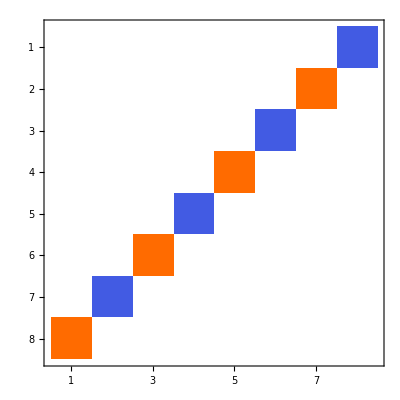
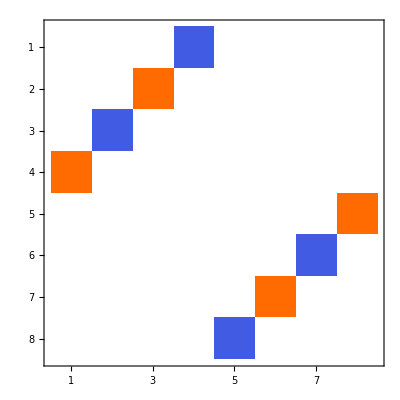
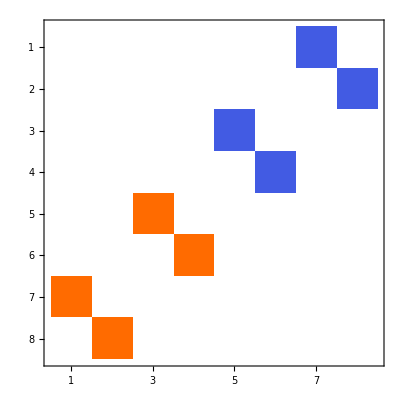
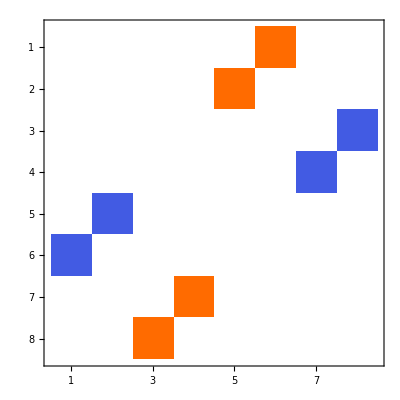
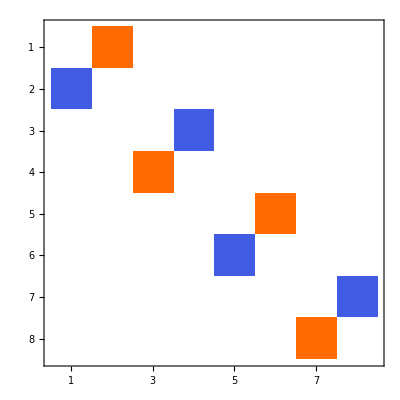
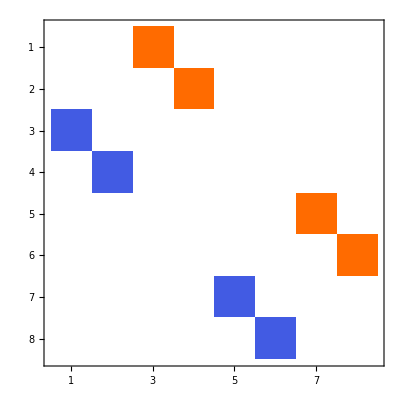

```mathematica
MatrixPlot/@vectors[testAlgebra,1]
```

where orange represents positive and blue negative numbers. Squares of the matrices gives minus unit matrix

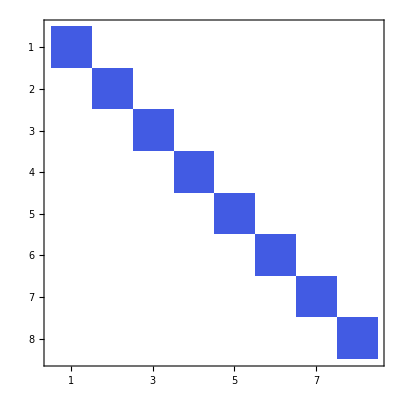
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[0, 6, 0]

{(x$22432[1]^2+x$22432[2]^2+x$22432[3]^2+x$22432[4]^2+x$22432[5]^2+x$22432[6]^2)^4,(x$22432[1]^2+x$22432[2]^2+x$22432[3]^2+x$22432[4]^2+x$22432[5]^2+x$22432[6]^2)^4}

#### Cl[0,7], ->ℝ(8)⊕ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[0,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100020200020

Base vector matrix representations. The  default setting,

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[2,0]->"IPauli[3,1]",Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},QuaternionIsomorphismRules->True},gaGradesOnly->{1}])
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 100020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 100020200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

The ℝ(8)⊕ℝ(8) structure is more clearly seen from

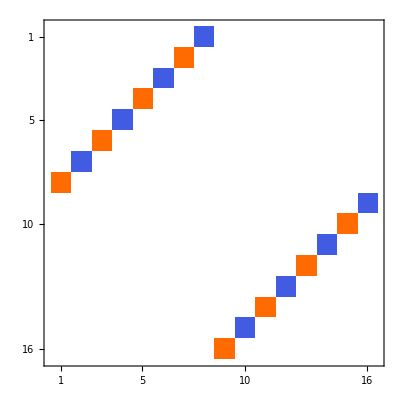
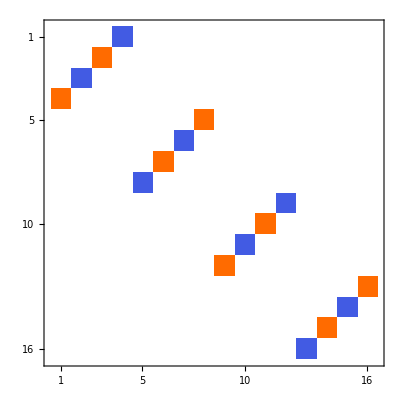
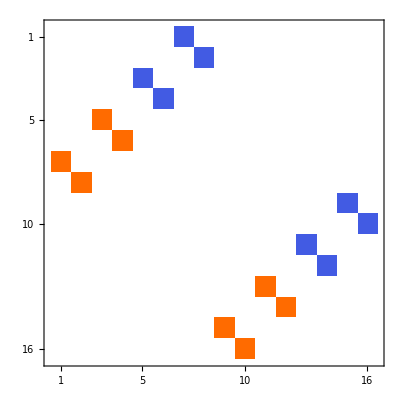
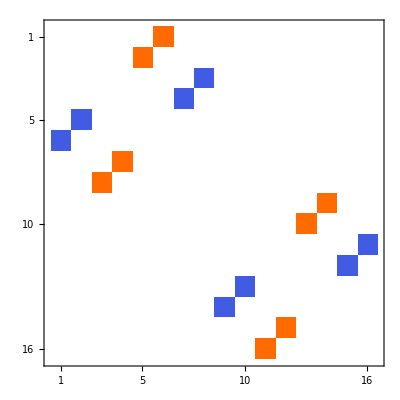
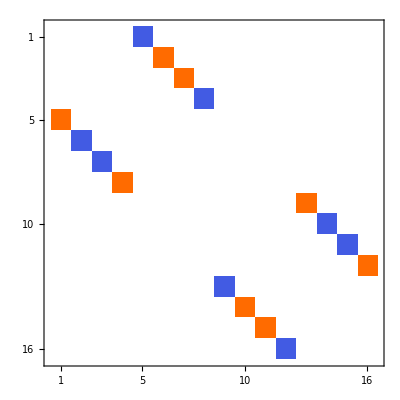
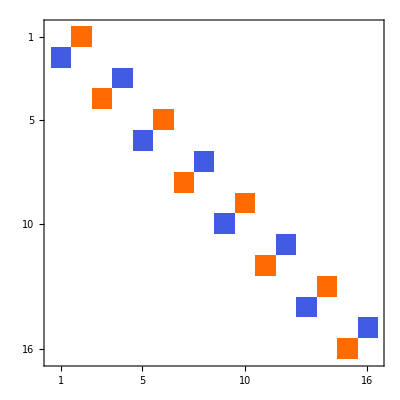
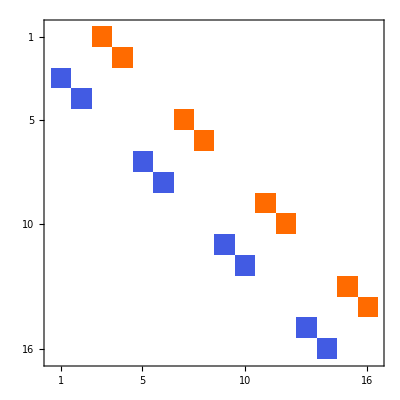

```mathematica
MatrixPlot/@vectors[testAlgebra,1]
```

These again squares to minus diagonal matrices

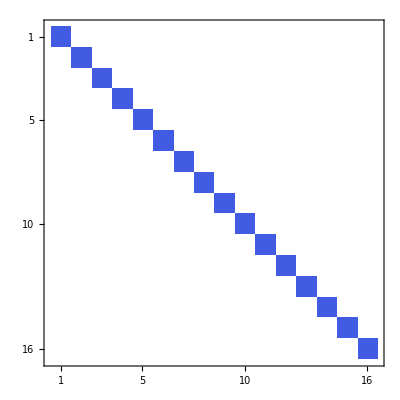
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[0, 7, 0]

{(x$23543[1]^2+x$23543[2]^2+x$23543[3]^2+x$23543[4]^2+x$23543[5]^2+x$23543[6]^2+x$23543[7]^2)^8,(x$23543[1]^2+x$23543[2]^2+x$23543[3]^2+x$23543[4]^2+x$23543[5]^2+x$23543[6]^2+x$23543[7]^2)^8}

#### Cl[1,2], ->ℂ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010110

Base vector matrix representations. The  default setting,

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"}},gaGradesOnly->{1}])
```

Basis vectors of 010110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(1 | 0
0 | -1),(0 | ⅈ
ⅈ | 0),(0 | 1
-1 | 0)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[1, 2, 0]

{-x$23645[1]^2+x$23645[2]^2+x$23645[3]^2,-x$23645[1]^2+x$23645[2]^2+x$23645[3]^2}

#### Cl[1,3], ->ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020110

Base vector matrix quaternionic representations.

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(1 | 0
0 | -1),(0 | 1020Quaternion
1020Quaternion | 0),(0 | 2020Quaternion
2020Quaternion | 0),(0 | 1
-1 | 0)}

Squares of quaternionic matrices can be calculated as

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0
0 | 1),(-1 | 0
0 | -1),(-1 | 0
0 | -1),(-1 | 0
0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[1, 3, 0]

{-x$23749[1]^2+x$23749[2]^2+x$23749[3]^2+x$23749[4]^2,-x$23749[1]^2+x$23749[2]^2+x$23749[3]^2+x$23749[4]^2}

Complex matrices can be calculated as

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,1]->"Antisymmetric",Cl[0,2]->"Pauli[1,2]"}},gaGradesOnly->{1}])
```

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,2])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{(x$23798[1]^2-x$23798[2]^2-x$23798[3]^2-x$23798[4]^2)^2,(x$23798[1]^2-x$23798[2]^2-x$23798[3]^2-x$23798[4]^2)^2}

Or even symbolically as (one of many variants)

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,1]->"Trigonometric",Cl[0,2]->"HyperbolicTrigonometric"}},gaGradesOnly->{1}])//Simplify
```

{(Sin[φ$23828] | Cos[φ$23828] | 0 | 0
Cos[φ$23828] | -Sin[φ$23828] | 0 | 0
0 | 0 | Sin[φ$23828] | Cos[φ$23828]
0 | 0 | Cos[φ$23828] | -Sin[φ$23828]),(0 | -ⅈ Sinh[φ$23820] | 0 | Cosh[φ$23820]
ⅈ Sinh[φ$23820] | 0 | -Cosh[φ$23820] | 0
0 | Cosh[φ$23820] | 0 | ⅈ Sinh[φ$23820]
-Cosh[φ$23820] | 0 | -ⅈ Sinh[φ$23820] | 0),(0 | Cosh[φ$23820] | 0 | ⅈ Sinh[φ$23820]
-Cosh[φ$23820] | 0 | -ⅈ Sinh[φ$23820] | 0
0 | ⅈ Sinh[φ$23820] | 0 | -Cosh[φ$23820]
-ⅈ Sinh[φ$23820] | 0 | Cosh[φ$23820] | 0),(-ⅈ Cos[φ$23828] | ⅈ Sin[φ$23828] | 0 | 0
ⅈ Sin[φ$23828] | ⅈ Cos[φ$23828] | 0 | 0
0 | 0 | -ⅈ Cos[φ$23828] | ⅈ Sin[φ$23828]
0 | 0 | ⅈ Sin[φ$23828] | ⅈ Cos[φ$23828])}

```mathematica
MatrixForm/@Simplify[(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,3])]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{(x$23850[1]^2-x$23850[2]^2-x$23850[3]^2-x$23850[4]^2)^2,(x$23850[1]^2-x$23850[2]^2-x$23850[3]^2-x$23850[4]^2)^2}

#### Cl[1,4], ->ℍ(2)⊕ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100020110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 100020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | -12020Quaternion | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[1, 4, 0]

{(x$23979[1]^2-x$23979[2]^2-x$23979[3]^2-x$23979[4]^2-x$23979[5]^2)^2,(x$23979[1]^2-x$23979[2]^2-x$23979[3]^2-x$23979[4]^2-x$23979[5]^2)^2}

#### Cl[1,5], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200020110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 200020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | -12020Quaternion | 0),(0 | 0 | 0 | 12020Quaternion
0 | 0 | 12020Quaternion | 0
0 | 12020Quaternion | 0 | 0
12020Quaternion | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of quaternionic matrices can be calculated as

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[1, 5, 0]

{(x$24139[1]^2-x$24139[2]^2-x$24139[3]^2-x$24139[4]^2-x$24139[5]^2-x$24139[6]^2)^2,(x$24139[1]^2-x$24139[2]^2-x$24139[3]^2-x$24139[4]^2-x$24139[5]^2-x$24139[6]^2)^2}

#### Cl[1,6], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010200020110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 010200020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of  matrices can be calculated as

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[1, 6, 0]

{(x$24312[1]^2-x$24312[2]^2-x$24312[3]^2-x$24312[4]^2-x$24312[5]^2-x$24312[6]^2-x$24312[7]^2)^4,(x$24312[1]^2-x$24312[2]^2-x$24312[3]^2-x$24312[4]^2-x$24312[5]^2-x$24312[6]^2-x$24312[7]^2)^4}

#### Cl[1,7], ->ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[1,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020200020110

Base vector matrix representations using default settings

Basis vectors of 020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 020200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

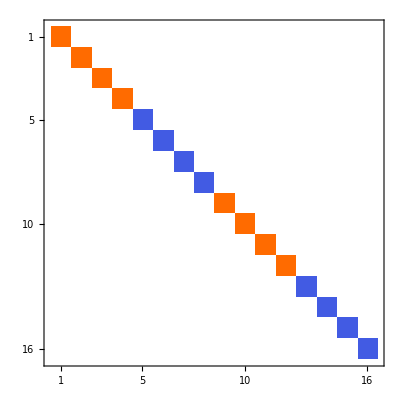
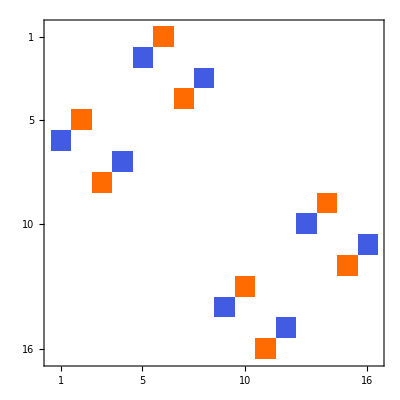
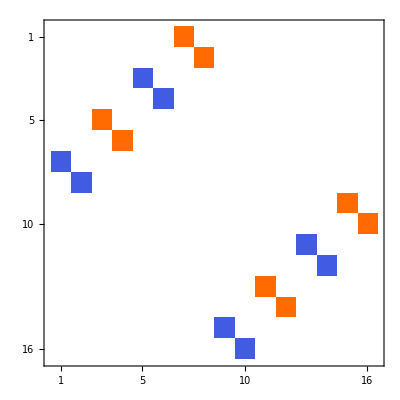
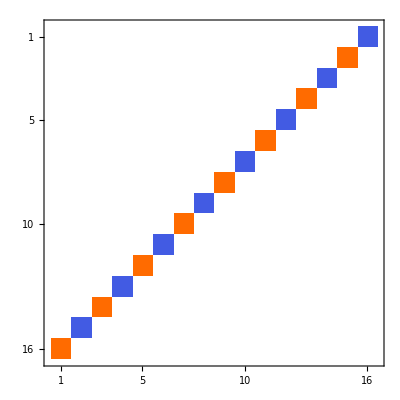
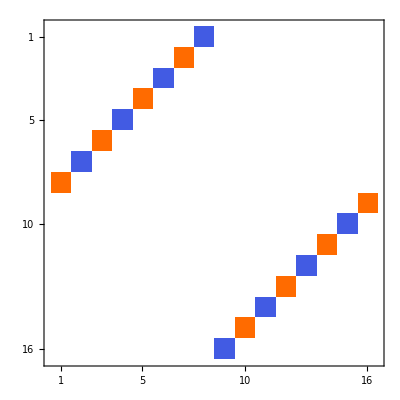
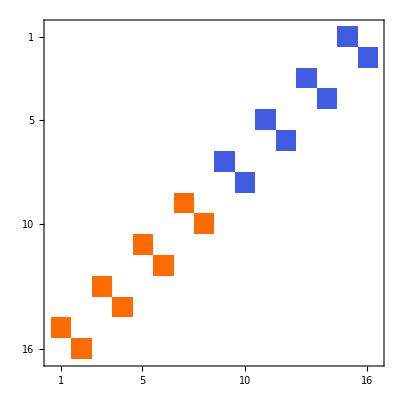
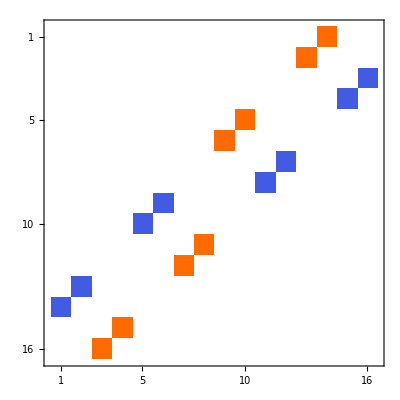
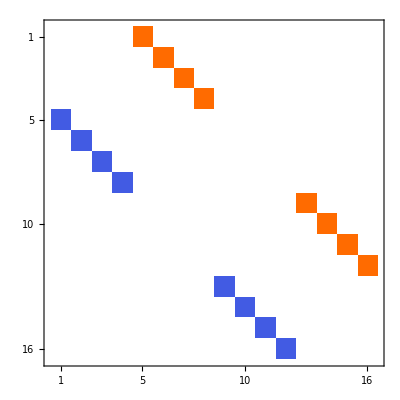

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",QuaternionIsomorphismRules->True},gaGradesOnly->{1}])
```

We can make them sparse with

```mathematica
vectors[testAlgebra,2]=SparseArray/@vectors[testAlgebra,1]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunately gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

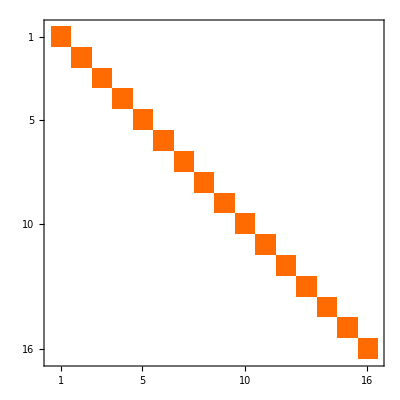
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(Dot[#,#]&/@vectors[testAlgebra,2])
```

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[1, 7, 0]

{(x$26034[1]^2-x$26034[2]^2-x$26034[3]^2-x$26034[4]^2-x$26034[5]^2-x$26034[6]^2-x$26034[7]^2-x$26034[8]^2)^8,(x$26034[1]^2-x$26034[2]^2-x$26034[3]^2-x$26034[4]^2-x$26034[5]^2-x$26034[6]^2-x$26034[7]^2-x$26034[8]^2)^8}

#### Cl[2,1], ->ℝ(2)⊕ℝ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",QuaternionIsomorphismRules->True},gaGradesOnly->{1}])
```

Basis vectors of 100110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{1}].

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→1,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

There exist, however 2×2 dimensional real representation!  These representations are not universal (see Jayme Vaz, Jr.; Roldao Da Rocha, Jr. “An Introduction to Clifford Algebras and Spinors”, 2016,Oxford.

```mathematica
MapAt[MatrixForm,(vectors[testAlgebra,2]=gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"},QuaternionIsomorphismRules->True,BaseVectorAlgebra->Cl[1,2],TargetMatrices->Reals},gaGradesOnly->{1}]),{All,2}]
```

{1210→(0 | -1
-1 | 0),2210→(1 | 0
0 | -1),3210→(0 | 1
-1 | 0)}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunately gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

```mathematica
MatrixForm/@(MapAt[Dot[#,#]&,vectors[testAlgebra,2],{All,2}])
```

{1210→{{1,0},{0,1}},2210→{{1,0},{0,1}},3210→{{-1,0},{0,-1}}}

Test the interesting determinant property for both vectors representations (note the difference in powers)

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$26249[1]^2+x$26249[2]^2-x$26249[3]^2)^2,(x$26249[1]^2+x$26249[2]^2-x$26249[3]^2)^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{-x$26257[1]^2-x$26257[2]^2+x$26257[3]^2,-x$26257[1]^2-x$26257[2]^2+x$26257[3]^2}

#### Cl[2,2], ->ℝ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunately gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[2, 2, 0]

{(x$26356[1]^2+x$26356[2]^2-x$26356[3]^2-x$26356[4]^2)^2,(x$26356[1]^2+x$26356[2]^2-x$26356[3]^2-x$26356[4]^2)^2}

#### Cl[2,3], ->ℂ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using Dot[ ]. Unfortunately gaGeometricMatrixProduct[ ] would expand them to dense matrix and it will take much more time to multiply

```mathematica
MatrixForm/@(Dot[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$26481[1]^2+x$26481[2]^2-x$26481[3]^2-x$26481[4]^2-x$26481[5]^2)^2,(x$26481[1]^2+x$26481[2]^2-x$26481[3]^2-x$26481[4]^2-x$26481[5]^2)^2}

#### Cl[2,4], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 020110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0
0 | 1020Quaternion | 0 | 0
1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0
0 | 2020Quaternion | 0 | 0
2020Quaternion | 0 | 0 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[2, 4, 0]

{(x$26629[1]^2+x$26629[2]^2-x$26629[3]^2-x$26629[4]^2-x$26629[5]^2-x$26629[6]^2)^2,(x$26629[1]^2+x$26629[2]^2-x$26629[3]^2-x$26629[4]^2-x$26629[5]^2-x$26629[6]^2)^2}

#### Cl[2,5], ->ℍ(4)⊕ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 100020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100020110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

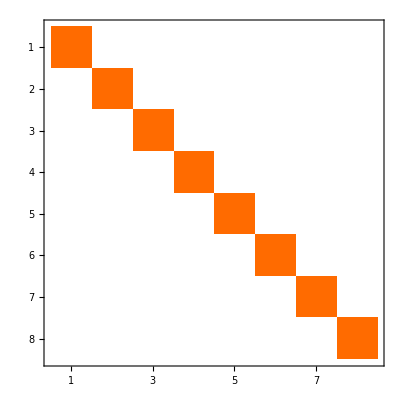
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[2, 5, 0]

{(x$27390[1]^2+x$27390[2]^2-x$27390[3]^2-x$27390[4]^2-x$27390[5]^2-x$27390[6]^2-x$27390[7]^2)^4,(x$27390[1]^2+x$27390[2]^2-x$27390[3]^2-x$27390[4]^2-x$27390[5]^2-x$27390[6]^2-x$27390[7]^2)^4}

#### Cl[2,6], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 200020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[2, 6, 0]

{(x$27620[1]^2+x$27620[2]^2-x$27620[3]^2-x$27620[4]^2-x$27620[5]^2-x$27620[6]^2-x$27620[7]^2-x$27620[8]^2)^4,(x$27620[1]^2+x$27620[2]^2-x$27620[3]^2-x$27620[4]^2-x$27620[5]^2-x$27620[6]^2-x$27620[7]^2-x$27620[8]^2)^4}

#### Cl[2,7], ->ℂ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[2,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010200020110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 010200020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[2, 7, 0]

{(x$28418[1]^2+x$28418[2]^2-x$28418[3]^2-x$28418[4]^2-x$28418[5]^2-x$28418[6]^2-x$28418[7]^2-x$28418[8]^2-x$28418[9]^2)^8,(x$28418[1]^2+x$28418[2]^2-x$28418[3]^2-x$28418[4]^2-x$28418[5]^2-x$28418[6]^2-x$28418[7]^2-x$28418[8]^2-x$28418[9]^2)^8}

#### Cl[3,0], ->ℂ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1},BasisVectorsReordering->{2,3,1}])
```

{(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | ⅈ
-ⅈ | 0)}

Base vector matrix representations using symbolic matrix. Possible  types are "Trigonometric"
"TrigonometricAntisymmetric"
"HyperbolicTrigonometric"
"HyperbolicTrigonometricAntisymmetric"

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{010->"Complex",200->"Trigonometric"}},gaGradesOnly->{1}])
```

{(0 | ⅈ (Cos[φ$28544]^2+Sin[φ$28544]^2)
ⅈ (-Cos[φ$28544]^2-Sin[φ$28544]^2) | 0),(Sin[φ$28544] | Cos[φ$28544]
Cos[φ$28544] | -Sin[φ$28544]),(-Cos[φ$28544] | Sin[φ$28544]
Sin[φ$28544] | Cos[φ$28544])}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]//Simplify)
```

{(0 | ⅈ
-ⅈ | 0),(Sin[φ$28544] | Cos[φ$28544]
Cos[φ$28544] | -Sin[φ$28544]),(-Cos[φ$28544] | Sin[φ$28544]
Sin[φ$28544] | Cos[φ$28544])}

The other form is

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{010->"Complex",200->"HyperbolicTrigonometric"}},gaGradesOnly->{1}])
```

{(0 | ⅈ (-Cosh[φ$29200]^2+Sinh[φ$29200]^2)
ⅈ (Cosh[φ$29200]^2-Sinh[φ$29200]^2) | 0),(-ⅈ Sinh[φ$29200] | Cosh[φ$29200]
Cosh[φ$29200] | ⅈ Sinh[φ$29200]),(Cosh[φ$29200] | ⅈ Sinh[φ$29200]
ⅈ Sinh[φ$29200] | -Cosh[φ$29200])}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]//Simplify)
```

{(0 | -ⅈ
ⅈ | 0),(-ⅈ Sinh[φ$29200] | Cosh[φ$29200]
Cosh[φ$29200] | ⅈ Sinh[φ$29200]),(Cosh[φ$29200] | ⅈ Sinh[φ$29200]
ⅈ Sinh[φ$29200] | -Cosh[φ$29200])}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
MatrixForm/@(Simplify[gaGeometricMatrixProduct[#,#]]&/@vectors[testAlgebra,2])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
MatrixForm/@(Simplify[gaGeometricMatrixProduct[#,#]]&/@vectors[testAlgebra,3])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{-x$29241[1]^2-x$29241[2]^2-x$29241[3]^2,-x$29241[1]^2-x$29241[2]^2-x$29241[3]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{-x$29243[1]^2-x$29243[2]^2-x$29243[3]^2,-x$29243[1]^2-x$29243[2]^2-x$29243[3]^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,3],testAlgebra,False]
```

{-x$29245[1]^2-x$29245[2]^2-x$29245[3]^2,-x$29245[1]^2-x$29245[2]^2-x$29245[3]^2}

Matrix determinant computation for complex algebras

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

{(0 | ⅈ
-ⅈ | 0),(1 | 0
0 | -1),(0 | 1
1 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=ArrayFlatten[#,2]&/@(vectors[testAlgebra,1]/.{0->{{0,0},{0,0}},1->{{1,0},{0,1}},-1->{{-1,0},{0,-1}},-I->{{0,-1},{1,0}},I->{{0,1},{-1,0}}}))
```

{(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)}

```mathematica
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra= Cl[3, 0, 0]

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
gaDefineMatrixRepresentation[Table[𝕖[i]->vectors[testAlgebra,2][[i]],{i,3}]]
```

{1300→{{0,0,0,1},{0,0,-1,0},{0,-1,0,0},{1,0,0,0}},2300→{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},3300→{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},12300→{{0,0,0,-1},{0,0,1,0},{0,-1,0,0},{1,0,0,0}},13300→{{0,1,0,0},{-1,0,0,0},{0,0,0,-1},{0,0,1,0}},23300→{{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}},123300→{{0,-1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,1,0}}}

```mathematica
Det[gaToMatrixRepresentation[gaGeneralMultivector[a,testAlgebra],testAlgebra]]
gaDeterminantOfMV[gaGeneralMultivector[a,testAlgebra]]-%//Expand
```

a[0]^4-2 a[0]^2 a[1]^2+a[1]^4-2 a[0]^2 a[2]^2+2 a[1]^2 a[2]^2+a[2]^4-2 a[0]^2 a[3]^2+2 a[1]^2 a[3]^2+2 a[2]^2 a[3]^2+a[3]^4+2 a[0]^2 a[4]^2-2 a[1]^2 a[4]^2-2 a[2]^2 a[4]^2+2 a[3]^2 a[4]^2+a[4]^4-8 a[2] a[3] a[4] a[5]+2 a[0]^2 a[5]^2-2 a[1]^2 a[5]^2+2 a[2]^2 a[5]^2-2 a[3]^2 a[5]^2+2 a[4]^2 a[5]^2+a[5]^4+8 a[1] a[3] a[4] a[6]-8 a[1] a[2] a[5] a[6]+2 a[0]^2 a[6]^2+2 a[1]^2 a[6]^2-2 a[2]^2 a[6]^2-2 a[3]^2 a[6]^2+2 a[4]^2 a[6]^2+2 a[5]^2 a[6]^2+a[6]^4-8 a[0] a[3] a[4] a[7]+8 a[0] a[2] a[5] a[7]-8 a[0] a[1] a[6] a[7]+2 a[0]^2 a[7]^2+2 a[1]^2 a[7]^2+2 a[2]^2 a[7]^2+2 a[3]^2 a[7]^2-2 a[4]^2 a[7]^2-2 a[5]^2 a[7]^2-2 a[6]^2 a[7]^2+a[7]^4

0

#### Cl[3,1], ->ℝ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[3, 1, 0]

{(x$29395[1]^2+x$29395[2]^2+x$29395[3]^2-x$29395[4]^2)^2,(x$29395[1]^2+x$29395[2]^2+x$29395[3]^2-x$29395[4]^2)^2}

#### Cl[3,2], ->ℝ(4)⊕ℝ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→2,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[3, 2, 0]

{(x$29533[1]^2+x$29533[2]^2+x$29533[3]^2-x$29533[4]^2-x$29533[5]^2)^4,(x$29533[1]^2+x$29533[2]^2+x$29533[3]^2-x$29533[4]^2-x$29533[5]^2)^4}

#### Cl[3,3], ->ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[3, 3, 0]

{(x$29666[1]^2+x$29666[2]^2+x$29666[3]^2-x$29666[4]^2-x$29666[5]^2-x$29666[6]^2)^4,(x$29666[1]^2+x$29666[2]^2+x$29666[3]^2-x$29666[4]^2-x$29666[5]^2-x$29666[6]^2)^4}

#### Cl[3,4], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[3, 4, 0]

{(x$29829[1]^2+x$29829[2]^2+x$29829[3]^2-x$29829[4]^2-x$29829[5]^2-x$29829[6]^2-x$29829[7]^2)^4,(x$29829[1]^2+x$29829[2]^2+x$29829[3]^2-x$29829[4]^2-x$29829[5]^2-x$29829[6]^2-x$29829[7]^2)^4}

#### Cl[3,5], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 020110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[3, 5, 0]

{(x$30051[1]^2+x$30051[2]^2+x$30051[3]^2-x$30051[4]^2-x$30051[5]^2-x$30051[6]^2-x$30051[7]^2-x$30051[8]^2)^4,(x$30051[1]^2+x$30051[2]^2+x$30051[3]^2-x$30051[4]^2-x$30051[5]^2-x$30051[6]^2-x$30051[7]^2-x$30051[8]^2)^4}

#### Cl[3,6], ->ℍ(8)⊕ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100020110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 100020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100020110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[3, 6, 0]

{(x$30332[1]^2+x$30332[2]^2+x$30332[3]^2-x$30332[4]^2-x$30332[5]^2-x$30332[6]^2-x$30332[7]^2-x$30332[8]^2-x$30332[9]^2)^8,(x$30332[1]^2+x$30332[2]^2+x$30332[3]^2-x$30332[4]^2-x$30332[5]^2-x$30332[6]^2-x$30332[7]^2-x$30332[8]^2-x$30332[9]^2)^8}

#### Cl[3,7], ->ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[3,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200020110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 200020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ]. Note, that Dot[ ] don’t know how to multiply quaternions

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representation. Now result is too large to factor, so calculate just difference

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,True]
```

Running algebra is: gaRunningAlgebra= Cl[3, 7, 0]

0

#### Cl[4,0], ->ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1020Quaternion
-1020Quaternion | 0),(0 | 2020Quaternion
-2020Quaternion | 0),(1 | 0
0 | -1),(0 | 1
1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1),(1 | 0
0 | 1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[4, 0, 0]

{-x$30742[1]^2-x$30742[2]^2-x$30742[3]^2-x$30742[4]^2,-x$30742[1]^2-x$30742[2]^2-x$30742[3]^2-x$30742[4]^2}

#### Cl[4,1], ->ℂ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[4, 1, 0]

{(x$30865[1]^2+x$30865[2]^2+x$30865[3]^2+x$30865[4]^2-x$30865[5]^2)^2,(x$30865[1]^2+x$30865[2]^2+x$30865[3]^2+x$30865[4]^2-x$30865[5]^2)^2}

#### Cl[4,2], ->ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 200110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[4, 2, 0]

{(x$30996[1]^2+x$30996[2]^2+x$30996[3]^2+x$30996[4]^2-x$30996[5]^2-x$30996[6]^2)^4,(x$30996[1]^2+x$30996[2]^2+x$30996[3]^2+x$30996[4]^2-x$30996[5]^2-x$30996[6]^2)^4}

#### Cl[4,3], ->ℝ(8)⊕ℝ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→3,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[4, 3, 0]

{(x$31625[1]^2+x$31625[2]^2+x$31625[3]^2+x$31625[4]^2-x$31625[5]^2-x$31625[6]^2-x$31625[7]^2)^8,(x$31625[1]^2+x$31625[2]^2+x$31625[3]^2+x$31625[4]^2-x$31625[5]^2-x$31625[6]^2-x$31625[7]^2)^8}

#### Cl[4,4], ->ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[4, 4, 0]

{(x$32317[1]^2+x$32317[2]^2+x$32317[3]^2+x$32317[4]^2-x$32317[5]^2-x$32317[6]^2-x$32317[7]^2-x$32317[8]^2)^8,(x$32317[1]^2+x$32317[2]^2+x$32317[3]^2+x$32317[4]^2-x$32317[5]^2-x$32317[6]^2-x$32317[7]^2-x$32317[8]^2)^8}

#### Cl[4,5], ->ℂ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[4, 5, 0]

{(x$33103[1]^2+x$33103[2]^2+x$33103[3]^2+x$33103[4]^2-x$33103[5]^2-x$33103[6]^2-x$33103[7]^2-x$33103[8]^2-x$33103[9]^2)^8,(x$33103[1]^2+x$33103[2]^2+x$33103[3]^2+x$33103[4]^2-x$33103[5]^2-x$33103[6]^2-x$33103[7]^2-x$33103[8]^2-x$33103[9]^2)^8}

#### Cl[4,6], ->ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020110110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 020110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[4, 6, 0]

{(x$34038[1]^2+x$34038[2]^2+x$34038[3]^2+x$34038[4]^2-x$34038[5]^2-x$34038[6]^2-x$34038[7]^2-x$34038[8]^2-x$34038[9]^2-x$34038[10]^2)^8,(x$34038[1]^2+x$34038[2]^2+x$34038[3]^2+x$34038[4]^2-x$34038[5]^2-x$34038[6]^2-x$34038[7]^2-x$34038[8]^2-x$34038[9]^2-x$34038[10]^2)^8}

#### Cl[4,7], ->ℍ(16)⊕ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100020110110110110

Base vector matrix representations using default settings

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 100020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100020110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

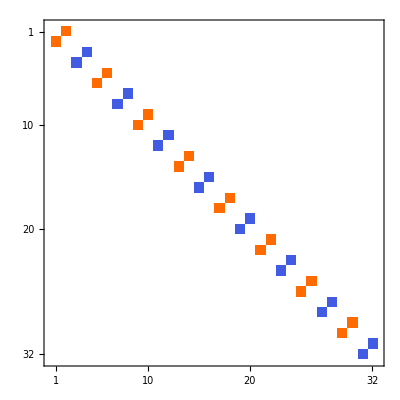
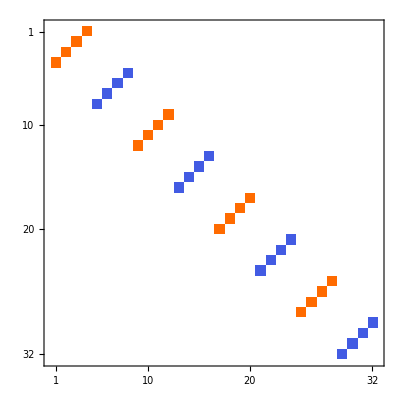
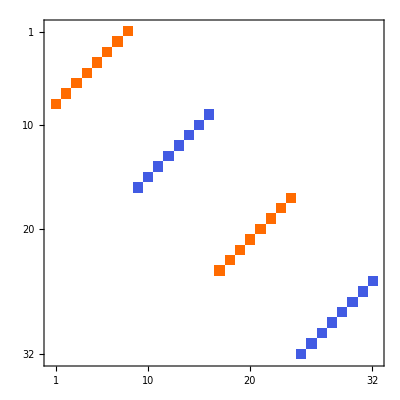
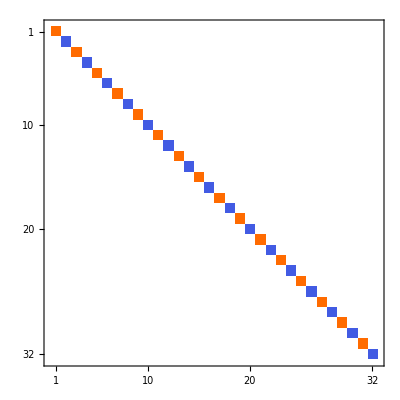
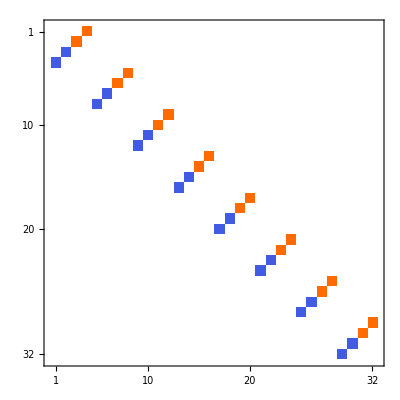
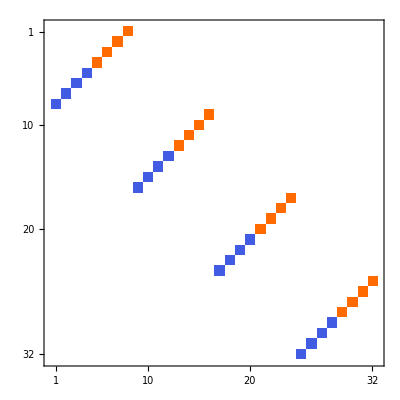
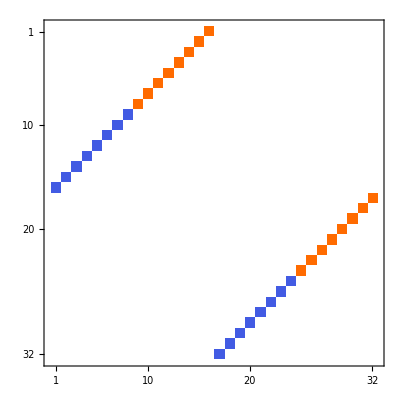
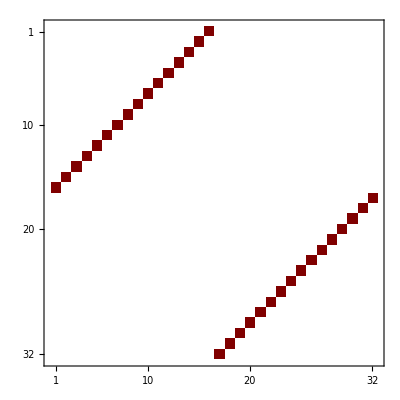
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

It is easy to see that dark red entries correspond to quaternions (i.𝕖. symbolic entries)

```mathematica
vectors[testAlgebra,1][[8]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1020Quaternion,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

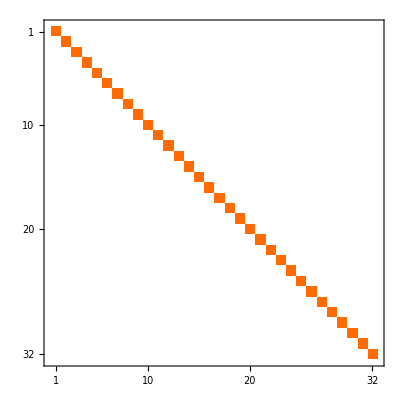
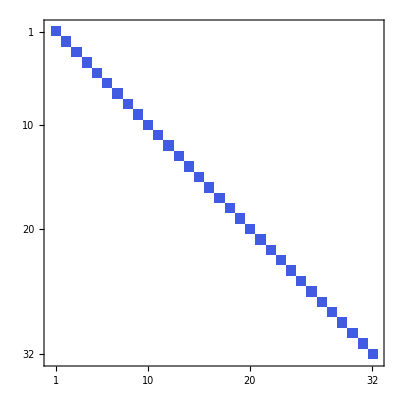
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[4, 7, 0]

{(x$35798[1]^2+x$35798[2]^2+x$35798[3]^2+x$35798[4]^2-x$35798[5]^2-x$35798[6]^2-x$35798[7]^2-x$35798[8]^2-x$35798[9]^2-x$35798[10]^2-x$35798[11]^2)^16,(x$35798[1]^2+x$35798[2]^2+x$35798[3]^2+x$35798[4]^2-x$35798[5]^2-x$35798[6]^2-x$35798[7]^2-x$35798[8]^2-x$35798[9]^2-x$35798[10]^2-x$35798[11]^2)^16}

#### Cl[5,0], ->ℍ(2)⊕ℍ(2)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 100020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1020Quaternion | 0 | 0
-1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | -1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
-2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | -2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
-12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | 12020Quaternion | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[5, 0, 0]

{(x$35931[1]^2+x$35931[2]^2+x$35931[3]^2+x$35931[4]^2+x$35931[5]^2)^2,(x$35931[1]^2+x$35931[2]^2+x$35931[3]^2+x$35931[4]^2+x$35931[5]^2)^2}

#### Cl[5,1], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 020200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion
0 | 0 | 1020Quaternion | 0
0 | -1020Quaternion | 0 | 0
-1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion
0 | 0 | 2020Quaternion | 0
0 | -2020Quaternion | 0 | 0
-2020Quaternion | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Test the interesting determinant property for  vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[5, 1, 0]

{(x$36084[1]^2+x$36084[2]^2+x$36084[3]^2+x$36084[4]^2+x$36084[5]^2-x$36084[6]^2)^2,(x$36084[1]^2+x$36084[2]^2+x$36084[3]^2+x$36084[4]^2+x$36084[5]^2-x$36084[6]^2)^2}

#### Cl[5,2], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010200110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[5, 2, 0]

{(x$36255[1]^2+x$36255[2]^2+x$36255[3]^2+x$36255[4]^2+x$36255[5]^2-x$36255[6]^2-x$36255[7]^2)^4,(x$36255[1]^2+x$36255[2]^2+x$36255[3]^2+x$36255[4]^2+x$36255[5]^2-x$36255[6]^2-x$36255[7]^2)^4}

#### Cl[5,3], ->ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200110110110

Base vector matrix representations using default settings

Basis vectors of 200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 200110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

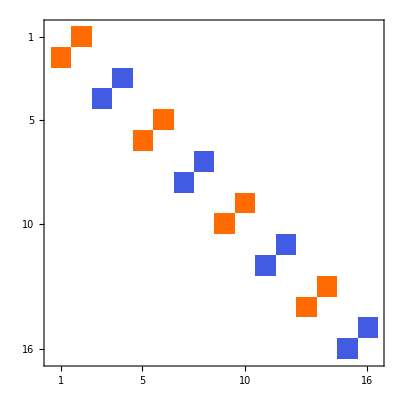
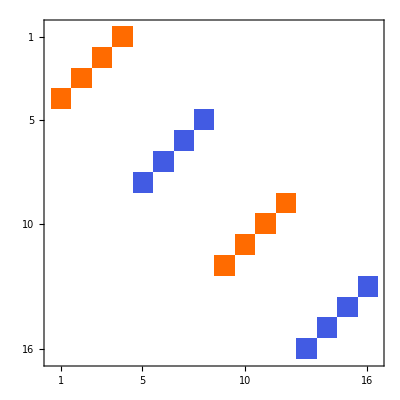
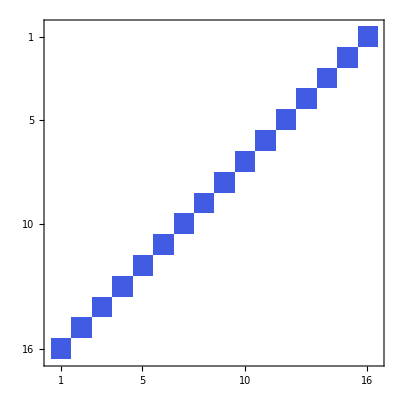
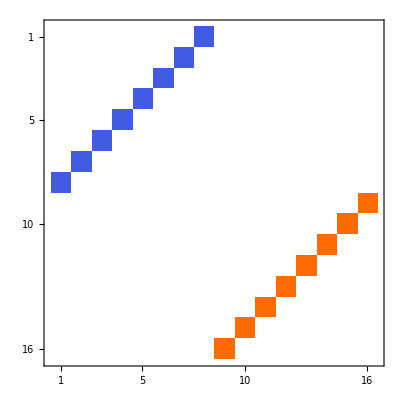
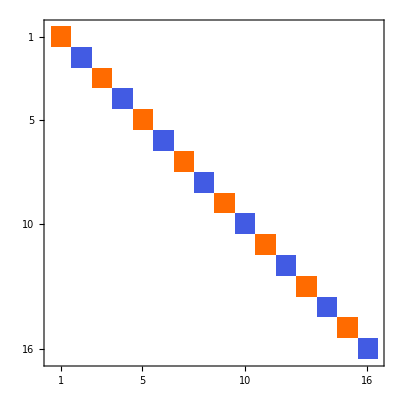
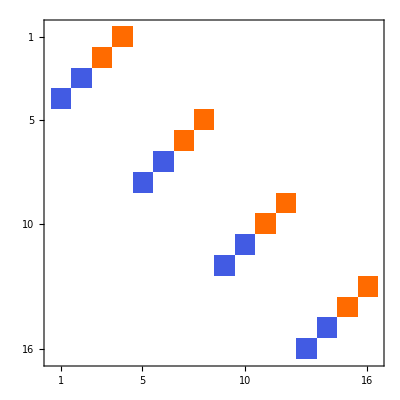
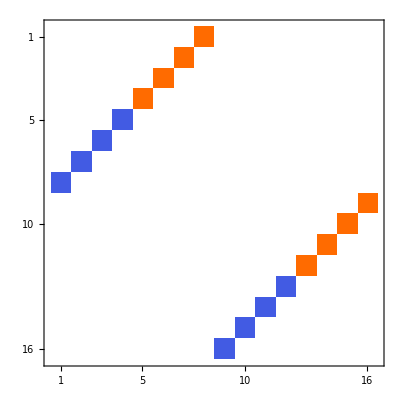
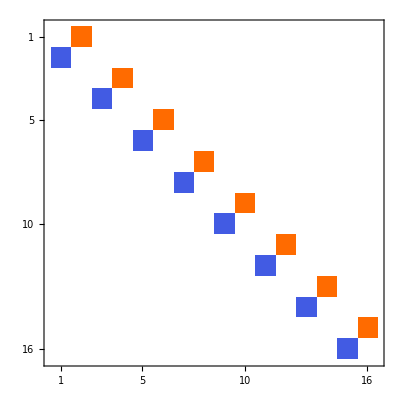

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[5, 3, 0]

{(x$37446[1]^2+x$37446[2]^2+x$37446[3]^2+x$37446[4]^2+x$37446[5]^2-x$37446[6]^2-x$37446[7]^2-x$37446[8]^2)^8,(x$37446[1]^2+x$37446[2]^2+x$37446[3]^2+x$37446[4]^2+x$37446[5]^2-x$37446[6]^2-x$37446[7]^2-x$37446[8]^2)^8}

#### Cl[5,4], ->ℝ(16)⊕ℝ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→4,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[5, 4, 0]

{(x$38833[1]^2+x$38833[2]^2+x$38833[3]^2+x$38833[4]^2+x$38833[5]^2-x$38833[6]^2-x$38833[7]^2-x$38833[8]^2-x$38833[9]^2)^16,(x$38833[1]^2+x$38833[2]^2+x$38833[3]^2+x$38833[4]^2+x$38833[5]^2-x$38833[6]^2-x$38833[7]^2-x$38833[8]^2-x$38833[9]^2)^16}

#### Cl[5,5], ->ℝ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

110110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  Dot[ ].

```mathematica
MatrixPlot/@(Dot[#,#]&/@(SparseArray/@vectors[testAlgebra,1]))
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[5, 5, 0]

{(x$40346[1]^2+x$40346[2]^2+x$40346[3]^2+x$40346[4]^2+x$40346[5]^2-x$40346[6]^2-x$40346[7]^2-x$40346[8]^2-x$40346[9]^2-x$40346[10]^2)^16,(x$40346[1]^2+x$40346[2]^2+x$40346[3]^2+x$40346[4]^2+x$40346[5]^2-x$40346[6]^2-x$40346[7]^2-x$40346[8]^2-x$40346[9]^2-x$40346[10]^2)^16}

#### Cl[5,6], ->ℂ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010110110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[5, 6, 0]

(-x$42024[1]^2-x$42024[2]^2-x$42024[3]^2-x$42024[4]^2-x$42024[5]^2+x$42024[6]^2+x$42024[7]^2+x$42024[8]^2+x$42024[9]^2+x$42024[10]^2+x$42024[11]^2)^16

#### Cl[5,7], ->ℍ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[5,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020110110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 020110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[5, 7, 0]

(-x$43940[1]^2-x$43940[2]^2-x$43940[3]^2-x$43940[4]^2-x$43940[5]^2+x$43940[6]^2+x$43940[7]^2+x$43940[8]^2+x$43940[9]^2+x$43940[10]^2+x$43940[11]^2+x$43940[12]^2)^16

#### Cl[6,0], ->ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 200020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1020Quaternion | 0 | 0
-1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion
0 | 0 | -1020Quaternion | 0),(0 | 2020Quaternion | 0 | 0
-2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion
0 | 0 | -2020Quaternion | 0),(0 | 12020Quaternion | 0 | 0
-12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -12020Quaternion
0 | 0 | 12020Quaternion | 0),(0 | 0 | 0 | 12020Quaternion
0 | 0 | -12020Quaternion | 0
0 | 12020Quaternion | 0 | 0
-12020Quaternion | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[6, 0, 0]

{(x$44095[1]^2+x$44095[2]^2+x$44095[3]^2+x$44095[4]^2+x$44095[5]^2+x$44095[6]^2)^2,(x$44095[1]^2+x$44095[2]^2+x$44095[3]^2+x$44095[4]^2+x$44095[5]^2+x$44095[6]^2)^2}

#### Cl[6,1], ->ℍ(4)⊕ℍ(4)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100020200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 100020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 100020200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[6, 1, 0]

{(x$44284[1]^2+x$44284[2]^2+x$44284[3]^2+x$44284[4]^2+x$44284[5]^2+x$44284[6]^2-x$44284[7]^2)^4,(x$44284[1]^2+x$44284[2]^2+x$44284[3]^2+x$44284[4]^2+x$44284[5]^2+x$44284[6]^2-x$44284[7]^2)^4}

#### Cl[6,2], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020200110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 020200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[6, 2, 0]

{(x$44504[1]^2+x$44504[2]^2+x$44504[3]^2+x$44504[4]^2+x$44504[5]^2+x$44504[6]^2-x$44504[7]^2-x$44504[8]^2)^4,(x$44504[1]^2+x$44504[2]^2+x$44504[3]^2+x$44504[4]^2+x$44504[5]^2+x$44504[6]^2-x$44504[7]^2-x$44504[8]^2)^4}

#### Cl[6,3], ->ℂ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010200110110110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010200110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[6, 3, 0]

{(x$45300[1]^2+x$45300[2]^2+x$45300[3]^2+x$45300[4]^2+x$45300[5]^2+x$45300[6]^2-x$45300[7]^2-x$45300[8]^2-x$45300[9]^2)^8,(x$45300[1]^2+x$45300[2]^2+x$45300[3]^2+x$45300[4]^2+x$45300[5]^2+x$45300[6]^2-x$45300[7]^2-x$45300[8]^2-x$45300[9]^2)^8}

#### Cl[6,4], ->ℝ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200110110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 200110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[6, 4, 0]

(-x$46813[1]^2-x$46813[2]^2-x$46813[3]^2-x$46813[4]^2-x$46813[5]^2-x$46813[6]^2+x$46813[7]^2+x$46813[8]^2+x$46813[9]^2+x$46813[10]^2)^16

#### Cl[6,5], ->ℝ(32)⊕ℝ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→5,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[6, 5, 0]

(-x$48530[1]^2-x$48530[2]^2-x$48530[3]^2-x$48530[4]^2-x$48530[5]^2-x$48530[6]^2+x$48530[7]^2+x$48530[8]^2+x$48530[9]^2+x$48530[10]^2+x$48530[11]^2)^32

#### Cl[6,6], ->ℝ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[6, 6, 0]

(-x$50373[1]^2-x$50373[2]^2-x$50373[3]^2-x$50373[4]^2-x$50373[5]^2-x$50373[6]^2+x$50373[7]^2+x$50373[8]^2+x$50373[9]^2+x$50373[10]^2+x$50373[11]^2+x$50373[12]^2)^32

#### Cl[6,7], ->ℂ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[6,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[6, 7, 0]

(-x$52387[1]^2-x$52387[2]^2-x$52387[3]^2-x$52387[4]^2-x$52387[5]^2-x$52387[6]^2+x$52387[7]^2+x$52387[8]^2+x$52387[9]^2+x$52387[10]^2+x$52387[11]^2+x$52387[12]^2+x$52387[13]^2)^32

#### Cl[7,0], ->ℂ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010200020200

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 010200020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[7, 0, 0]

{(x$52553[1]^2+x$52553[2]^2+x$52553[3]^2+x$52553[4]^2+x$52553[5]^2+x$52553[6]^2+x$52553[7]^2)^4,(x$52553[1]^2+x$52553[2]^2+x$52553[3]^2+x$52553[4]^2+x$52553[5]^2+x$52553[6]^2+x$52553[7]^2)^4}

#### Cl[7,1], ->ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200020200110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 200020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -1020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -2020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
-12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixForm/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[7, 1, 0]

{(x$52759[1]^2+x$52759[2]^2+x$52759[3]^2+x$52759[4]^2+x$52759[5]^2+x$52759[6]^2+x$52759[7]^2-x$52759[8]^2)^4,(x$52759[1]^2+x$52759[2]^2+x$52759[3]^2+x$52759[4]^2+x$52759[5]^2+x$52759[6]^2+x$52759[7]^2-x$52759[8]^2)^4}

#### Cl[7,2], ->ℍ(8)⊕ℍ(8)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100020200110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 100020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 100020200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[7, 2, 0]

{(x$54156[1]^2+x$54156[2]^2+x$54156[3]^2+x$54156[4]^2+x$54156[5]^2+x$54156[6]^2+x$54156[7]^2-x$54156[8]^2-x$54156[9]^2)^8,(x$54156[1]^2+x$54156[2]^2+x$54156[3]^2+x$54156[4]^2+x$54156[5]^2+x$54156[6]^2+x$54156[7]^2-x$54156[8]^2-x$54156[9]^2)^8}

#### Cl[7,3], ->ℍ(16)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,3];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020200110110110

Base vector matrix representations using default settings

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 020200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

Running algebra is: gaRunningAlgebra= Cl[7, 3, 0]

{(x$55721[1]^2+x$55721[2]^2+x$55721[3]^2+x$55721[4]^2+x$55721[5]^2+x$55721[6]^2+x$55721[7]^2-x$55721[8]^2-x$55721[9]^2-x$55721[10]^2)^8,(x$55721[1]^2+x$55721[2]^2+x$55721[3]^2+x$55721[4]^2+x$55721[5]^2+x$55721[6]^2+x$55721[7]^2-x$55721[8]^2-x$55721[9]^2-x$55721[10]^2)^8}

#### Cl[7,4], ->ℂ(32)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,4];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010200110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 010200110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The empty “matrix” has purely complex entries:

```mathematica
vectors[testAlgebra,1][[6]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[7, 4, 0]

(-x$57417[1]^2-x$57417[2]^2-x$57417[3]^2-x$57417[4]^2-x$57417[5]^2-x$57417[6]^2-x$57417[7]^2+x$57417[8]^2+x$57417[9]^2+x$57417[10]^2+x$57417[11]^2)^16

#### Cl[7,5], ->ℝ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

200110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 200110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[7, 5, 0]

(-x$59264[1]^2-x$59264[2]^2-x$59264[3]^2-x$59264[4]^2-x$59264[5]^2-x$59264[6]^2-x$59264[7]^2+x$59264[8]^2+x$59264[9]^2+x$59264[10]^2+x$59264[11]^2+x$59264[12]^2)^32

#### Cl[7,6], ->ℝ(64)⊕ℝ(64)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

100110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange poins are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 100110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 100110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→6,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[7, 6, 0]

(-x$61326[1]^2-x$61326[2]^2-x$61326[3]^2-x$61326[4]^2-x$61326[5]^2-x$61326[6]^2-x$61326[7]^2+x$61326[8]^2+x$61326[9]^2+x$61326[10]^2+x$61326[11]^2+x$61326[12]^2+x$61326[13]^2)^64

#### Cl[7,7], ->ℝ(128)

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[7,7];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

110110110110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 110110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 1, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford rezult

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[7, 7, 0]

(-x$63521[1]^2-x$63521[2]^2-x$63521[3]^2-x$63521[4]^2-x$63521[5]^2-x$63521[6]^2-x$63521[7]^2+x$63521[8]^2+x$63521[9]^2+x$63521[10]^2+x$63521[11]^2+x$63521[12]^2+x$63521[13]^2+x$63521[14]^2)^64

#### Cl[4,10]

Factor algebra into product of algebras

```mathematica
testAlgebra=Cl[4,10];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

020200020110110110110

Base vector matrix representations using default settings. Due to large matrix size we just plot matrix shapes (orange points are +1, blue represents -1)

```mathematica
MatrixPlot/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 020200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

General::stop: Further output of GeometricAlgebra`p`pickNextColor::maxColorLimit will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Squares of sparse matrices can be calculated using  gaGeometricMatrixProduct[ ].

```mathematica
MatrixPlot/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",QuaternionIsomorphismRules->True},gaGradesOnly->{1}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(gaGeometricMatrixProduct[#,#]&/@vectors[testAlgebra,1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Test the interesting determinant property. Calculation of matrix determinant  now takes too much memory, calculate only Clifford result

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False,onlyClifford->True]
```

Running algebra is: gaRunningAlgebra= Cl[4, 10, 0]

(-x$66918[1]^2-x$66918[2]^2-x$66918[3]^2-x$66918[4]^2+x$66918[5]^2+x$66918[6]^2+x$66918[7]^2+x$66918[8]^2+x$66918[9]^2+x$66918[10]^2+x$66918[11]^2+x$66918[12]^2+x$66918[13]^2+x$66918[14]^2)^64

### Some option usage examples

There are some options which can influence calculation of algebra matrix representations. Not all of them are useful.

```mathematica
Options[gaDefineMatrixRepresentation]
```

{Method→{TensorProduct},Quiet→False,BasisVectorsMultipliers→Automatic,gaGradesOnly→All,BasisVectorsReordering→None}

#### Option to reduce real representation size, Cl[2,1]

In the case when in algebra decomposition Cl_(1,0)appears one can choose matrices of less dimension (complex) matrices. For example

```mathematica
testAlgebra=Cl[2,1];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100110

Base vector matrix representations using default settings

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,gaGradesOnly->{1}])
```

gaDefineMatrixRepresentation::smaller: Tensor product decomposition 1 contains Cl[1,0] algebra. Smaller (complex) representation matrices can be obtained using Method ->{"TensorProduct",BaseVectorAlgebra→1,TargetMatrices→Reals}. The smaller matrices realizes HOMOMORPHISM of the algebra (not an isomorphism).

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

We are warned that factorized algebra Cl[2,1]->Cl[1,0]⊗Cl[1,2] contains Cl[1,0] algebra. In these cases we can reduce dimension of representation if complex matrices are allowed.  To find smaller representations of initial algebra Cl[2,1]  instead we use Cl[1,2] algebra (option BaseVectorAlgebra→Cl[1,2,0]) and multiply all obtained base vectors representations by imaginary unit. This will give representation of original Cl[2,1]. Indeed

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"},BaseVectorAlgebra->Cl[1,2,0],TargetMatrices->Reals},gaGradesOnly->{1}])
```

{(0 | -1
-1 | 0),(1 | 0
0 | -1),(0 | 1
-1 | 0)}

or

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,1]->"Complex",Cl[1,1]->"Antisymmetric"},BaseVectorAlgebra->Cl[1,2,0],TargetMatrices->Complexes},gaGradesOnly->{1}])
```

{(1 | 0
0 | -1),(0 | ⅈ
-ⅈ | 0),(0 | ⅈ
ⅈ | 0)}

if we prefer complex matrices (option TargetMatrices→Complex). This particular option simply sorts vectors by sign of their square, i.𝕖 matrices which squares to +1 goes first, then -1, and then inside each group sorts by complexes/reals property (i.e. real or complex matrices are preferred.

It is easy to see, that all obtained matrices generates representations of Cl[2,1]. Indeed Clifford property for base vectors 𝕖_i 𝕖_j+𝕖_j 𝕖_i=±2 δ_ij are satisfied.

```mathematica
Table[MatrixForm@(Dot[vectors[testAlgebra,1][[i]],vectors[testAlgebra,1][[j]]]+Dot[vectors[testAlgebra,1][[j]],vectors[testAlgebra,1][[i]]]),{i,3},{j,3}]
```

{{(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)},{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)}}

The smaller matrices generates not universal Clifford algebra, i.e. algebra, which has less that 2^n base elements. See below

```mathematica
Table[MatrixForm@(Dot[vectors[testAlgebra,2][[i]],vectors[testAlgebra,2][[j]]]+Dot[vectors[testAlgebra,2][[j]],vectors[testAlgebra,2][[i]]]),{i,3},{j,3}]
```

{{(2 | 0
0 | 2),(0 | 0
0 | 0),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(2 | 0
0 | 2),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(0 | 0
0 | 0),(-2 | 0
0 | -2)}}

```mathematica
Table[MatrixForm@(Dot[vectors[testAlgebra,3][[i]],vectors[testAlgebra,3][[j]]]+Dot[vectors[testAlgebra,3][[j]],vectors[testAlgebra,3][[i]]]),{i,3},{j,3}]
```

{{(2 | 0
0 | 2),(0 | 0
0 | 0),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(2 | 0
0 | 2),(0 | 0
0 | 0)},{(0 | 0
0 | 0),(0 | 0
0 | 0),(-2 | 0
0 | -2)}}

Calculate number of different elements for 210 we expect 2^3=8 elements (including identity matrix which is not computed below)

```mathematica
gaDefineOrthonormalBasis[testAlgebra]
```

Running algebra is: gaRunningAlgebra= Cl[2, 1, 0]

{1,1210,2210,3210,12210,13210,23210,123210}

```mathematica
MapAt[MatrixForm,matrices[testAlgebra,1]=gaDefineMatrixRepresentation[Thread[Rule[gaOrthonormalBasis[testAlgebra,{1}],vectors[testAlgebra,1]]]],{All,2}]
```

{1210→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),2210→(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),3210→(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),12210→(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),13210→(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),23210→(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),123210→(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

Indeed all 7 matrices, which represents basis elements are different and, therefore, the representation is universal (see Jayme Vaz, Jr.; Roldao Da Rocha, Jr. “An Introduction to Clifford Algebras and Spinors”, 2016,Oxford).

```mathematica
MatrixForm/@Union[Last/@matrices[testAlgebra,1]]
```

{(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)}

We see that in smaller representation we have less base elements! So these representations are not universal (see Jayme Vaz, Jr.; Roldao Da Rocha, Jr. “An Introduction to Clifford Algebras and Spinors”, 2016,Oxford.

```mathematica
MapAt[MatrixForm,matrices[testAlgebra,2]=gaDefineMatrixRepresentation[Thread[Rule[gaOrthonormalBasis[testAlgebra,{1}],vectors[testAlgebra,2]]]],{All,2}]
```

{1210→(0 | -1
-1 | 0),2210→(1 | 0
0 | -1),3210→(0 | 1
-1 | 0),12210→(0 | 1
-1 | 0),13210→(1 | 0
0 | -1),23210→(0 | 1
1 | 0),123210→(-1 | 0
0 | -1)}

For 2x2 matrices we have just 5 different matrices instead of 7!

```mathematica
MatrixForm/@Union[Last/@matrices[testAlgebra,2]]
```

{(-1 | 0
0 | -1),(0 | -1
-1 | 0),(0 | 1
-1 | 0),(0 | 1
1 | 0),(1 | 0
0 | -1)}

```mathematica
MapAt[MatrixForm,matrices[testAlgebra,3]=gaDefineMatrixRepresentation[Thread[Rule[gaOrthonormalBasis[testAlgebra,{1}],vectors[testAlgebra,3]]]],{All,2}]
```

{1210→(1 | 0
0 | -1),2210→(0 | ⅈ
-ⅈ | 0),3210→(0 | ⅈ
ⅈ | 0),12210→(0 | ⅈ
ⅈ | 0),13210→(0 | ⅈ
-ⅈ | 0),23210→(-1 | 0
0 | 1),123210→(-1 | 0
0 | -1)}

```mathematica
MatrixForm/@Union[Last/@matrices[testAlgebra,3]]
```

{(-1 | 0
0 | -1),(-1 | 0
0 | 1),(0 | ⅈ
-ⅈ | 0),(0 | ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

Test the interesting determinant property for both vectors representations

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,1],testAlgebra,False]
```

{(x$68576[1]^2+x$68576[2]^2-x$68576[3]^2)^2,(x$68576[1]^2+x$68576[2]^2-x$68576[3]^2)^2}

```mathematica
cliffordVectorsDeterminant[vectors[testAlgebra,2],testAlgebra,False]
```

{-x$68578[1]^2-x$68578[2]^2+x$68578[3]^2,-x$68578[1]^2-x$68578[2]^2+x$68578[3]^2}

#### Option to change algebra factorization

```mathematica
Options[gaToTensorProduct]
```

{ReductionOrder→{{110},{200,020}}}

```mathematica
testAlgebra=Cl[4,2];
reducedAlgebra[testAlgebra,1]=gaToTensorProduct[testAlgebra]
```

200110110

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,1],Method->{"TensorProduct",ElementaryRepresentations->{Cl[2,0]->"Symmetric",Cl[1,1]->"Antisymmetric"}},gaGradesOnly->{1}])
```

Basis vectors of 200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0]],{0, 1}].

Basis vectors of 200110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{1}].

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Using different factorizations we can get different matrix representations

```mathematica
reducedAlgebra[testAlgebra,2]=gaToTensorProduct[testAlgebra,ReductionOrder->{{Cl[2,0],Cl[0,2]},{Cl[1,1]}}]
```

200020020

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"}},gaGradesOnly->{1}])
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 200020020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[2, 0, 0], Cl[0, 2, 0], Cl[0, 2, 0]],{1}].

{(1020Quaternion⊗12020Quaternion | 0
0 | 1020Quaternion⊗12020Quaternion),(2020Quaternion⊗12020Quaternion | 0
0 | 2020Quaternion⊗12020Quaternion),(12020Quaternion⊗12020Quaternion | 0
0 | -(12020Quaternion⊗12020Quaternion)),(0 | 12020Quaternion⊗12020Quaternion
12020Quaternion⊗12020Quaternion | 0),(1⊗1020Quaternion | 0
0 | 1⊗1020Quaternion),(1⊗2020Quaternion | 0
0 | 1⊗2020Quaternion)}

Because here we see quaternion product, we can reduce them to real matrices with QuaternionIsomorphismRules→{“HH2R4”}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},QuaternionIsomorphismRules->{"HH2R4"}},gaGradesOnly->{1}])
```

{(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

Direct substitution of Pauli matrices with  QuaternionIsomorphismRules→{“Pauli[1,2]”} would not yield real matrices

```mathematica
MatrixForm/@(vectors[testAlgebra,4]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},QuaternionIsomorphismRules->{"Pauli[1,2]"}},gaGradesOnly->{1}])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

QuaternionIsomorphismRules→True is the same as QuaternionIsomorphismRules->{“HH2R4”,“Pauli[1,2]”}, i.𝕖 first apply quaternion product to real matrices, then if quaternions stil remains replace them by Pauli[1,2] matrices

```mathematica
reducedAlgebra[testAlgebra,2]
```

200020020

```mathematica
MatrixForm/@(vectors[testAlgebra,5]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]->"Symmetric"}},gaGradesOnly->{1}])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

BasisVectorsMultipliers->{{first algebra factor},{second algebra factor},...} will multiply that algebra column by given factor.

```mathematica
MatrixForm/@(vectors[testAlgebra,6]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Pauli[1,2]",Cl[2,0]->"Symmetric"}},gaGradesOnly->{1},BasisVectorsMultipliers->{{1,1},{1,1},{-1,1}}])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,7]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"}},gaGradesOnly->{1},BasisVectorsMultipliers->{{1,1},{1,1},{-1,1}}])
```

{(1020Quaternion⊗-12020Quaternion | 0
0 | 1020Quaternion⊗-12020Quaternion),(2020Quaternion⊗-12020Quaternion | 0
0 | 2020Quaternion⊗-12020Quaternion),(12020Quaternion⊗-12020Quaternion | 0
0 | -(12020Quaternion⊗-12020Quaternion)),(0 | 12020Quaternion⊗-12020Quaternion
12020Quaternion⊗-12020Quaternion | 0),(1⊗-1020Quaternion | 0
0 | 1⊗-1020Quaternion),(1⊗2020Quaternion | 0
0 | 1⊗2020Quaternion)}

```mathematica
MatrixForm/@(vectors[testAlgebra,8]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},QuaternionIsomorphismRules->{"HH2R4"}},gaGradesOnly->{1},BasisVectorsMultipliers->{{1,1},{1,1},{-1,1}}])
```

{(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,9]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},QuaternionIsomorphismRules->{"Pauli[1,2]"}},gaGradesOnly->{1},BasisVectorsMultipliers->{{1,1},{1,1},{-1,1}}])
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

This option might be useful investigating what elements change changing something in elementary representation.

#### Option to use different IsomorphismRules

```mathematica
testAlgebra=Cl[0,3];
```

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}}},gaGradesOnly->{1}])
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{1}].

{(12020Quaternion | 0
0 | -12020Quaternion),(1020Quaternion | 0
0 | 1020Quaternion),(2020Quaternion | 0
0 | 2020Quaternion)}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[0,2]->{"Q[1,2]"}},QuaternionIsomorphismRules->{"HH2R4","QToRealMatrix"}},gaGradesOnly->{1}])
```

{(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
testAlgebra=Cl[3,6];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

100020110110110

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[0,2]->{"Q[1,2]"}},QuaternionIsomorphismRules->{"HH2R4"}},gaGradesOnly->{1}])
```

Basis vectors of 100020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 100020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 100020110110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[1, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0], Cl[1, 1, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12020Quaternion | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

```mathematica
MatrixPlot/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[0,2]->{"Q[1,2]"}},QuaternionIsomorphismRules->{"HH2R4","QToRealMatrix"}},gaGradesOnly->{1}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct",ElementaryRepresentations->{Cl[1,0]->"Diagonal",Cl[1,1]->"Antisymmetric",Cl[0,2]->{"Q[1,2]"}},QuaternionIsomorphismRules->{"QToRealMatrix"}},gaGradesOnly->{1}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
vectors[testAlgebra,2]===vectors[testAlgebra,3]
```

True

Using different factorizations we can get different matrix representations

```mathematica
testAlgebra=Cl[4,2];
reducedAlgebra[testAlgebra,2]=gaToTensorProduct[testAlgebra,ReductionOrder->{{Cl[2,0],Cl[0,2]},{Cl[1,1]}}]
```

200020020

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"}},gaGradesOnly->{1}])
```

{(1020Quaternion⊗12020Quaternion | 0
0 | 1020Quaternion⊗12020Quaternion),(2020Quaternion⊗12020Quaternion | 0
0 | 2020Quaternion⊗12020Quaternion),(12020Quaternion⊗12020Quaternion | 0
0 | -(12020Quaternion⊗12020Quaternion)),(0 | 12020Quaternion⊗12020Quaternion
12020Quaternion⊗12020Quaternion | 0),(1⊗1020Quaternion | 0
0 | 1⊗1020Quaternion),(1⊗2020Quaternion | 0
0 | 1⊗2020Quaternion)}

Because here we see quaternion product, we can reduce them to real matrices with QuaternionIsomorphismRules→{“HH2R4”}

```mathematica
MatrixForm/@(vectors[testAlgebra,2]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},QuaternionIsomorphismRules->{"HH2R4"}},gaGradesOnly->{1}])
```

{(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,3]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},QuaternionIsomorphismRules->{"Pauli[1,2]"}},gaGradesOnly->{1}])
```

{(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)}

Usage of isomorphism rules “IToRealMatrix” is highly unrecommended. It might give false and unexpected results. Use on you own risk and always check.

```mathematica
MatrixForm/@(vectors[testAlgebra,4]=Last/@gaDefineMatrixRepresentation[reducedAlgebra[testAlgebra,2],Method->{"TensorProduct",ElementaryRepresentations->{Cl[0,2]->"Q[1,2]",Cl[2,0]->"Symmetric"},QuaternionIsomorphismRules->{"Pauli[1,2]","IToRealMatrix"}},gaGradesOnly->{1}])
```

gaDefineMatrixRepresentation::isomorphismIRule: Warning. Imaginary unit replacement "IToRealMatrix" was applied. It replaces explicitly elements ±1 and ±ⅈ. For general matrices it will definitely yield wrong result. Please check the answer explicitly or don't use "IToRealMatrix" rules!

General::stop: Further output of gaDefineMatrixRepresentation::isomorphismIRule will be suppressed during this calculation.

{(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0)}

### Hermite conjugate involution action tested on matrices (without conjugations the formulas applies for matrix transposition)

#### For Cl_(n,0) Hermitian conjugation is the same as reverse (simplest special case)

First, test that for Euclidean algebras Hermitian conjugation

```mathematica
testAlgebra=Cl[3,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

010200

```mathematica
fullSymbolicBase[testAlgebra]=gaDefineOrthonormalBasis[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Running algebra is: gaRunningAlgebra= Cl[3, 0, 0]

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
reversedSymbolicBase[testAlgebra]=gaReverse/@fullSymbolicBase[testAlgebra]
```

{1,1300,2300,3300,-12300,-13300,-23300,-123300}

```mathematica
signsAfterHermiteConjugateInvolution[testAlgebra]=reversedSymbolicBase[testAlgebra]/.𝕖[__]:>1
```

{1,1,1,1,-1,-1,-1,-1}

Now matrices: vector representations

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"},gaGradesOnly->{1}])
```

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{1}].

{(0 | ⅈ
-ⅈ | 0),(1 | 0
0 | -1),(0 | 1
1 | 0)}

All elements

```mathematica
MatrixForm/@(allElements[testAlgebra,1]=Prepend[Last/@gaDefineMatrixRepresentation[testAlgebra,Method->{"TensorProduct"}],IdentityMatrix[2]])
```

{(1 | 0
0 | 1),(0 | ⅈ
-ⅈ | 0),(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | -ⅈ
-ⅈ | 0),(ⅈ | 0
0 | -ⅈ),(0 | 1
-1 | 0),(-ⅈ | 0
0 | -ⅈ)}

Explicit matrix Hermite conjugation: the function conjugateHermiteConjugat[ ] is defined in the beginning of the notebook

```mathematica
MatrixForm/@(allElementsHC[testAlgebra,1]=conjugateHermiteConjugate/@allElements[testAlgebra,1])
```

{(1 | 0
0 | 1),(0 | ⅈ
-ⅈ | 0),(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | ⅈ
ⅈ | 0),(-ⅈ | 0
0 | ⅈ),(0 | -1
1 | 0),(ⅈ | 0
0 | ⅈ)}

Use signs of involution Hermite conjugation and subtract the two results. Zero matrices means we are done.

```mathematica
MatrixForm/@(signsAfterHermiteConjugateInvolution[testAlgebra]*allElements[testAlgebra,1]-allElementsHC[testAlgebra,1])
```

{(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0),(0 | 0
0 | 0)}

#### For Cl_(p,q) Hermitian conjugation, p is odd/Even J.Vaz “Clifford algebras and spinors”, (formulas 4.86/4.87), page 118

First, test that for Euclidean algebras Hermitian conjugation

```mathematica
testAlgebra=Cl[5,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 510are stored in variable gaOrthonormalBasis[Cl[5, 1, 0],InvDeg[Lex]].

```mathematica
A1Complex[testAlgebra]=gaGeneralMultivector[A,testAlgebra]/.A[_]:>RandomComplex[{-100-100*I,100+100*I}];
```

```mathematica
gaDefineMatrixRepresentation[testAlgebra]
```

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 020200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0]],{0, 1}].

GeometricAlgebra`p`pickNextColor::maxColorLimit: Smart color picking limit 15 was reached. Start picking colors randomly.

Basis vectors of 020200110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 2, 0], Cl[2, 0, 0], Cl[1, 1, 0]],{1}].

{1510→{{0,1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,-1,0}},2510→{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}},3510→{{0,0,0,1020Quaternion},{0,0,1020Quaternion,0},{0,-1020Quaternion,0,0},{-1020Quaternion,0,0,0}},4510→{{0,0,0,2020Quaternion},{0,0,2020Quaternion,0},{0,-2020Quaternion,0,0},{-2020Quaternion,0,0,0}},5510→{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},6510→{{0,1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,-1,0}},12510→{{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}},13510→{{0,0,1020Quaternion,0},{0,0,0,1020Quaternion},{1020Quaternion,0,0,0},{0,1020Quaternion,0,0}},14510→{{0,0,2020Quaternion,0},{0,0,0,2020Quaternion},{2020Quaternion,0,0,0},{0,2020Quaternion,0,0}},15510→{{0,-1,0,0},{1,0,0,0},{0,0,0,1},{0,0,-1,0}},16510→{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}},23510→{{-1020Quaternion,0,0,0},{0,-1020Quaternion,0,0},{0,0,1020Quaternion,0},{0,0,0,1020Quaternion}},24510→{{-2020Quaternion,0,0,0},{0,-2020Quaternion,0,0},{0,0,2020Quaternion,0},{0,0,0,2020Quaternion}},25510→{{0,0,0,-1},{0,0,1,0},{0,-1,0,0},{1,0,0,0}},26510→{{0,0,-1,0},{0,0,0,1},{-1,0,0,0},{0,1,0,0}},34510→{{-12020Quaternion,0,0,0},{0,-12020Quaternion,0,0},{0,0,-12020Quaternion,0},{0,0,0,-12020Quaternion}},35510→{{0,0,0,-1020Quaternion},{0,0,1020Quaternion,0},{0,1020Quaternion,0,0},{-1020Quaternion,0,0,0}},36510→{{0,0,-1020Quaternion,0},{0,0,0,1020Quaternion},{1020Quaternion,0,0,0},{0,-1020Quaternion,0,0}},45510→{{0,0,0,-2020Quaternion},{0,0,2020Quaternion,0},{0,2020Quaternion,0,0},{-2020Quaternion,0,0,0}},46510→{{0,0,-2020Quaternion,0},{0,0,0,2020Quaternion},{2020Quaternion,0,0,0},{0,-2020Quaternion,0,0}},56510→{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}},123510→{{0,-1020Quaternion,0,0},{-1020Quaternion,0,0,0},{0,0,0,-1020Quaternion},{0,0,-1020Quaternion,0}},124510→{{0,-2020Quaternion,0,0},{-2020Quaternion,0,0,0},{0,0,0,-2020Quaternion},{0,0,-2020Quaternion,0}},125510→{{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}},126510→{{0,0,0,1},{0,0,-1,0},{0,-1,0,0},{1,0,0,0}},134510→{{0,-12020Quaternion,0,0},{-12020Quaternion,0,0,0},{0,0,0,12020Quaternion},{0,0,12020Quaternion,0}},135510→{{0,0,1020Quaternion,0},{0,0,0,-1020Quaternion},{1020Quaternion,0,0,0},{0,-1020Quaternion,0,0}},136510→{{0,0,0,1020Quaternion},{0,0,-1020Quaternion,0},{0,1020Quaternion,0,0},{-1020Quaternion,0,0,0}},145510→{{0,0,2020Quaternion,0},{0,0,0,-2020Quaternion},{2020Quaternion,0,0,0},{0,-2020Quaternion,0,0}},146510→{{0,0,0,2020Quaternion},{0,0,-2020Quaternion,0},{0,2020Quaternion,0,0},{-2020Quaternion,0,0,0}},156510→{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},234510→{{0,0,0,-12020Quaternion},{0,0,-12020Quaternion,0},{0,-12020Quaternion,0,0},{-12020Quaternion,0,0,0}},235510→{{-1020Quaternion,0,0,0},{0,1020Quaternion,0,0},{0,0,1020Quaternion,0},{0,0,0,-1020Quaternion}},236510→{{0,-1020Quaternion,0,0},{1020Quaternion,0,0,0},{0,0,0,1020Quaternion},{0,0,-1020Quaternion,0}},245510→{{-2020Quaternion,0,0,0},{0,2020Quaternion,0,0},{0,0,2020Quaternion,0},{0,0,0,-2020Quaternion}},246510→{{0,-2020Quaternion,0,0},{2020Quaternion,0,0,0},{0,0,0,2020Quaternion},{0,0,-2020Quaternion,0}},256510→{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},345510→{{-12020Quaternion,0,0,0},{0,12020Quaternion,0,0},{0,0,-12020Quaternion,0},{0,0,0,12020Quaternion}},346510→{{0,-12020Quaternion,0,0},{12020Quaternion,0,0,0},{0,0,0,-12020Quaternion},{0,0,12020Quaternion,0}},356510→{{0,0,1020Quaternion,0},{0,0,0,1020Quaternion},{-1020Quaternion,0,0,0},{0,-1020Quaternion,0,0}},456510→{{0,0,2020Quaternion,0},{0,0,0,2020Quaternion},{-2020Quaternion,0,0,0},{0,-2020Quaternion,0,0}},1234510→{{0,0,-12020Quaternion,0},{0,0,0,-12020Quaternion},{12020Quaternion,0,0,0},{0,12020Quaternion,0,0}},1235510→{{0,1020Quaternion,0,0},{-1020Quaternion,0,0,0},{0,0,0,1020Quaternion},{0,0,-1020Quaternion,0}},1236510→{{1020Quaternion,0,0,0},{0,-1020Quaternion,0,0},{0,0,1020Quaternion,0},{0,0,0,-1020Quaternion}},1245510→{{0,2020Quaternion,0,0},{-2020Quaternion,0,0,0},{0,0,0,2020Quaternion},{0,0,-2020Quaternion,0}},1246510→{{2020Quaternion,0,0,0},{0,-2020Quaternion,0,0},{0,0,2020Quaternion,0},{0,0,0,-2020Quaternion}},1256510→{{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}},1345510→{{0,12020Quaternion,0,0},{-12020Quaternion,0,0,0},{0,0,0,-12020Quaternion},{0,0,12020Quaternion,0}},1346510→{{12020Quaternion,0,0,0},{0,-12020Quaternion,0,0},{0,0,-12020Quaternion,0},{0,0,0,12020Quaternion}},1356510→{{0,0,0,1020Quaternion},{0,0,1020Quaternion,0},{0,1020Quaternion,0,0},{1020Quaternion,0,0,0}},1456510→{{0,0,0,2020Quaternion},{0,0,2020Quaternion,0},{0,2020Quaternion,0,0},{2020Quaternion,0,0,0}},2345510→{{0,0,0,12020Quaternion},{0,0,-12020Quaternion,0},{0,12020Quaternion,0,0},{-12020Quaternion,0,0,0}},2346510→{{0,0,12020Quaternion,0},{0,0,0,-12020Quaternion},{12020Quaternion,0,0,0},{0,-12020Quaternion,0,0}},2356510→{{0,-1020Quaternion,0,0},{-1020Quaternion,0,0,0},{0,0,0,1020Quaternion},{0,0,1020Quaternion,0}},2456510→{{0,-2020Quaternion,0,0},{-2020Quaternion,0,0,0},{0,0,0,2020Quaternion},{0,0,2020Quaternion,0}},3456510→{{0,-12020Quaternion,0,0},{-12020Quaternion,0,0,0},{0,0,0,-12020Quaternion},{0,0,-12020Quaternion,0}},12345510→{{0,0,-12020Quaternion,0},{0,0,0,12020Quaternion},{12020Quaternion,0,0,0},{0,-12020Quaternion,0,0}},12346510→{{0,0,0,-12020Quaternion},{0,0,12020Quaternion,0},{0,12020Quaternion,0,0},{-12020Quaternion,0,0,0}},12356510→{{-1020Quaternion,0,0,0},{0,-1020Quaternion,0,0},{0,0,-1020Quaternion,0},{0,0,0,-1020Quaternion}},12456510→{{-2020Quaternion,0,0,0},{0,-2020Quaternion,0,0},{0,0,-2020Quaternion,0},{0,0,0,-2020Quaternion}},13456510→{{-12020Quaternion,0,0,0},{0,-12020Quaternion,0,0},{0,0,12020Quaternion,0},{0,0,0,12020Quaternion}},23456510→{{0,0,-12020Quaternion,0},{0,0,0,-12020Quaternion},{-12020Quaternion,0,0,0},{0,-12020Quaternion,0,0}},123456510→{{0,0,0,-12020Quaternion},{0,0,-12020Quaternion,0},{0,12020Quaternion,0,0},{12020Quaternion,0,0,0}}}

```mathematica
MatrixForm[(A1ComplexM[testAlgebra]=gaToMatrixRepresentation[A1Complex[testAlgebra],testAlgebra])]
```

((23.6323-159.333 ⅈ)+(50.2472+156.936 ⅈ) 1020Quaternion+(101.311-120.055 ⅈ) 2020Quaternion+(102.808+16.4486 ⅈ) 12020Quaternion | (48.5603+118.484 ⅈ)+(49.2072-63.5174 ⅈ) 1020Quaternion+(74.7065-58.0799 ⅈ) 2020Quaternion+(122.762-201.818 ⅈ) 12020Quaternion | (-106.915+93.5247 ⅈ)-(29.82+128.153 ⅈ) 1020Quaternion+(160.768-11.13 ⅈ) 2020Quaternion-(189.913-22.9589 ⅈ) 12020Quaternion | (116.921-115.003 ⅈ)+(5.60057+102.288 ⅈ) 1020Quaternion+(172.454+113.619 ⅈ) 2020Quaternion+(19.5353+128.047 ⅈ) 12020Quaternion
(-17.6019-84.9657 ⅈ)+(89.7172+254.773 ⅈ) 1020Quaternion-(111.139-172.329 ⅈ) 2020Quaternion-(60.132-143.366 ⅈ) 12020Quaternion | (-52.6702-11.1636 ⅈ)-(68.3714+69.3066 ⅈ) 1020Quaternion+(72.4465-7.87186 ⅈ) 2020Quaternion-(29.2964+25.3712 ⅈ) 12020Quaternion | (-153.496-37.5534 ⅈ)-(3.62983-27.2866 ⅈ) 1020Quaternion-(54.3694+33.6172 ⅈ) 2020Quaternion+(40.7477+153.73 ⅈ) 12020Quaternion | (-29.0964+22.4896 ⅈ)-(24.5461+136.123 ⅈ) 1020Quaternion-(12.0433+44.6835 ⅈ) 2020Quaternion-(74.0187-53.8529 ⅈ) 12020Quaternion
(120.687-106.708 ⅈ)+(31.4899-77.6321 ⅈ) 1020Quaternion-(179.95-44.3912 ⅈ) 2020Quaternion+(128.242+231.126 ⅈ) 12020Quaternion | (34.1736-162.948 ⅈ)-(63.965+99.1836 ⅈ) 1020Quaternion-(152.111+13.388 ⅈ) 2020Quaternion+(132.073+119.282 ⅈ) 12020Quaternion | (-188.494+104.226 ⅈ)+(8.70871-120.169 ⅈ) 1020Quaternion+(127.679-30.6711 ⅈ) 2020Quaternion+(127.815-71.4232 ⅈ) 12020Quaternion | (39.4782+153.562 ⅈ)-(139.274+79.3875 ⅈ) 1020Quaternion-(13.16-76.3566 ⅈ) 2020Quaternion-(62.5882+135.732 ⅈ) 12020Quaternion
(-54.2502+77.409 ⅈ)-(187.103+110.791 ⅈ) 1020Quaternion+(14.5122-87.0566 ⅈ) 2020Quaternion+(46.1759-13.8579 ⅈ) 12020Quaternion | (-124.112+182.014 ⅈ)-(0.155839-187.446 ⅈ) 1020Quaternion-(7.83726-99.3107 ⅈ) 2020Quaternion-(59.3952+129.428 ⅈ) 12020Quaternion | (301.783+65.8033 ⅈ)-(58.5923+90.2546 ⅈ) 1020Quaternion+(71.8083+23.431 ⅈ) 2020Quaternion-(40.9914+86.8924 ⅈ) 12020Quaternion | (-162.867+82.8008 ⅈ)+(205.911-138.415 ⅈ) 1020Quaternion+(24.3151+169.474 ⅈ) 2020Quaternion+(115.655-263.155 ⅈ) 12020Quaternion)

```mathematica
MatrixForm[lhs[testAlgebra]=ConjugateTranspose[A1ComplexM[testAlgebra]]/.Conjugate->gaQuaternionicConjugate]
```

((23.6323+159.333 ⅈ)-(50.2472-156.936 ⅈ) 1020Quaternion-(101.311+120.055 ⅈ) 2020Quaternion-(102.808-16.4486 ⅈ) 12020Quaternion | (-17.6019+84.9657 ⅈ)-(89.7172-254.773 ⅈ) 1020Quaternion+(111.139+172.329 ⅈ) 2020Quaternion+(60.132+143.366 ⅈ) 12020Quaternion | (120.687+106.708 ⅈ)-(31.4899+77.6321 ⅈ) 1020Quaternion+(179.95+44.3912 ⅈ) 2020Quaternion-(128.242-231.126 ⅈ) 12020Quaternion | (-54.2502-77.409 ⅈ)+(187.103-110.791 ⅈ) 1020Quaternion-(14.5122+87.0566 ⅈ) 2020Quaternion-(46.1759+13.8579 ⅈ) 12020Quaternion
(48.5603-118.484 ⅈ)-(49.2072+63.5174 ⅈ) 1020Quaternion-(74.7065+58.0799 ⅈ) 2020Quaternion-(122.762+201.818 ⅈ) 12020Quaternion | (-52.6702+11.1636 ⅈ)+(68.3714-69.3066 ⅈ) 1020Quaternion-(72.4465+7.87186 ⅈ) 2020Quaternion+(29.2964-25.3712 ⅈ) 12020Quaternion | (34.1736+162.948 ⅈ)+(63.965-99.1836 ⅈ) 1020Quaternion+(152.111-13.388 ⅈ) 2020Quaternion-(132.073-119.282 ⅈ) 12020Quaternion | (-124.112-182.014 ⅈ)+(0.155839+187.446 ⅈ) 1020Quaternion+(7.83726+99.3107 ⅈ) 2020Quaternion+(59.3952-129.428 ⅈ) 12020Quaternion
(-106.915-93.5247 ⅈ)+(29.82-128.153 ⅈ) 1020Quaternion-(160.768+11.13 ⅈ) 2020Quaternion+(189.913+22.9589 ⅈ) 12020Quaternion | (-153.496+37.5534 ⅈ)+(3.62983+27.2866 ⅈ) 1020Quaternion+(54.3694-33.6172 ⅈ) 2020Quaternion-(40.7477-153.73 ⅈ) 12020Quaternion | (-188.494-104.226 ⅈ)-(8.70871+120.169 ⅈ) 1020Quaternion-(127.679+30.6711 ⅈ) 2020Quaternion-(127.815+71.4232 ⅈ) 12020Quaternion | (301.783-65.8033 ⅈ)+(58.5923-90.2546 ⅈ) 1020Quaternion-(71.8083-23.431 ⅈ) 2020Quaternion+(40.9914-86.8924 ⅈ) 12020Quaternion
(116.921+115.003 ⅈ)-(5.60057-102.288 ⅈ) 1020Quaternion-(172.454-113.619 ⅈ) 2020Quaternion-(19.5353-128.047 ⅈ) 12020Quaternion | (-29.0964-22.4896 ⅈ)+(24.5461-136.123 ⅈ) 1020Quaternion+(12.0433-44.6835 ⅈ) 2020Quaternion+(74.0187+53.8529 ⅈ) 12020Quaternion | (39.4782-153.562 ⅈ)+(139.274-79.3875 ⅈ) 1020Quaternion+(13.16+76.3566 ⅈ) 2020Quaternion+(62.5882-135.732 ⅈ) 12020Quaternion | (-162.867-82.8008 ⅈ)-(205.911+138.415 ⅈ) 1020Quaternion-(24.3151-169.474 ⅈ) 2020Quaternion-(115.655+263.155 ⅈ) 12020Quaternion)

```mathematica
MatrixForm[rhs[testAlgebra]=gaToMatrixRepresentation[If[OddQ[testAlgebra[[1]]],
gaIndexDown[gaInverse[𝕖[mvDownUp[Range[1,testAlgebra[[1]]],{}],testAlgebra]]]\[GeometricProduct]gaComplexConjugate[gaReverse[A1Complex[testAlgebra]]]\[GeometricProduct]𝕖[mvDownUp[Range[1,testAlgebra[[1]]],{}],testAlgebra]
,
gaIndexDown[gaInverse[𝕖[mvDownUp[Range[1,testAlgebra[[1]]],{}],testAlgebra]]]\[GeometricProduct]gaComplexConjugate[gaGradeInverse[gaReverse[A1Complex[testAlgebra]]]]\[GeometricProduct]𝕖[mvDownUp[Range[1,testAlgebra[[1]]],{}],testAlgebra]
]//gaPE,testAlgebra]]
```

((23.6323+159.333 ⅈ)-(50.2472-156.936 ⅈ) 1020Quaternion-(101.311+120.055 ⅈ) 2020Quaternion-(102.808-16.4486 ⅈ) 12020Quaternion | (-17.6019+84.9657 ⅈ)-(89.7172-254.773 ⅈ) 1020Quaternion+(111.139+172.329 ⅈ) 2020Quaternion+(60.132+143.366 ⅈ) 12020Quaternion | (120.687+106.708 ⅈ)-(31.4899+77.6321 ⅈ) 1020Quaternion+(179.95+44.3912 ⅈ) 2020Quaternion-(128.242-231.126 ⅈ) 12020Quaternion | (-54.2502-77.409 ⅈ)+(187.103-110.791 ⅈ) 1020Quaternion-(14.5122+87.0566 ⅈ) 2020Quaternion-(46.1759+13.8579 ⅈ) 12020Quaternion
(48.5603-118.484 ⅈ)-(49.2072+63.5174 ⅈ) 1020Quaternion-(74.7065+58.0799 ⅈ) 2020Quaternion-(122.762+201.818 ⅈ) 12020Quaternion | (-52.6702+11.1636 ⅈ)+(68.3714-69.3066 ⅈ) 1020Quaternion-(72.4465+7.87186 ⅈ) 2020Quaternion+(29.2964-25.3712 ⅈ) 12020Quaternion | (34.1736+162.948 ⅈ)+(63.965-99.1836 ⅈ) 1020Quaternion+(152.111-13.388 ⅈ) 2020Quaternion-(132.073-119.282 ⅈ) 12020Quaternion | (-124.112-182.014 ⅈ)+(0.155839+187.446 ⅈ) 1020Quaternion+(7.83726+99.3107 ⅈ) 2020Quaternion+(59.3952-129.428 ⅈ) 12020Quaternion
(-106.915-93.5247 ⅈ)+(29.82-128.153 ⅈ) 1020Quaternion-(160.768+11.13 ⅈ) 2020Quaternion+(189.913+22.9589 ⅈ) 12020Quaternion | (-153.496+37.5534 ⅈ)+(3.62983+27.2866 ⅈ) 1020Quaternion+(54.3694-33.6172 ⅈ) 2020Quaternion-(40.7477-153.73 ⅈ) 12020Quaternion | (-188.494-104.226 ⅈ)-(8.70871+120.169 ⅈ) 1020Quaternion-(127.679+30.6711 ⅈ) 2020Quaternion-(127.815+71.4232 ⅈ) 12020Quaternion | (301.783-65.8033 ⅈ)+(58.5923-90.2546 ⅈ) 1020Quaternion-(71.8083-23.431 ⅈ) 2020Quaternion+(40.9914-86.8924 ⅈ) 12020Quaternion
(116.921+115.003 ⅈ)-(5.60057-102.288 ⅈ) 1020Quaternion-(172.454-113.619 ⅈ) 2020Quaternion-(19.5353-128.047 ⅈ) 12020Quaternion | (-29.0964-22.4896 ⅈ)+(24.5461-136.123 ⅈ) 1020Quaternion+(12.0433-44.6835 ⅈ) 2020Quaternion+(74.0187+53.8529 ⅈ) 12020Quaternion | (39.4782-153.562 ⅈ)+(139.274-79.3875 ⅈ) 1020Quaternion+(13.16+76.3566 ⅈ) 2020Quaternion+(62.5882-135.732 ⅈ) 12020Quaternion | (-162.867-82.8008 ⅈ)-(205.911+138.415 ⅈ) 1020Quaternion-(24.3151-169.474 ⅈ) 2020Quaternion-(115.655+263.155 ⅈ) 12020Quaternion)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

#### For Cl_(p,q) Hermitian conjugation, q is odd/Even J.Vaz “Clifford algebras and spinors”, (formulas 4.88/4.89), page 118

First, test that for Euclidean algebras Hermitian conjugation

```mathematica
testAlgebra=Cl[2,7];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

Basis vectors of 270are stored in variable gaOrthonormalBasis[Cl[2, 7, 0],InvDeg[Lex]].

```mathematica
A1Complex[testAlgebra]=gaGeneralMultivector[A,testAlgebra]/.A[_]:>RandomComplex[{-100-100*I,100+100*I}];
```

```mathematica
gaDefineMatrixRepresentation[testAlgebra];
```

Basis vectors of 010are stored in variable gaOrthonormalBasis[Cl[0, 1, 0],InvDeg[Lex],{0, 1}].

Basis vectors of 010200are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Basis vectors of 010200020are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{0, 1}].

Basis vectors of 010200020110are stored in variable gaOrthonormalBasis[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0], Cl[1, 1, 0]],{0, 1}].

```mathematica
MatrixForm[(A1ComplexM[testAlgebra]=gaToMatrixRepresentation[A1Complex[testAlgebra],testAlgebra])]
```

(126.638-77.9534 ⅈ | -240.457-136.705 ⅈ | -20.9004-29.7098 ⅈ | 142.576-286.932 ⅈ | -395.995-306.051 ⅈ | -299.764+484.044 ⅈ | 259.78+43.4948 ⅈ | 580.806+484.702 ⅈ | 51.9793-320.376 ⅈ | -229.18-179.326 ⅈ | -343.736+172.797 ⅈ | 115.894-2.29291 ⅈ | 374.746+347.059 ⅈ | 168.285+62. ⅈ | -82.7394+224.759 ⅈ | 217.053-582.574 ⅈ
-173.974+698.115 ⅈ | -102.363+250.027 ⅈ | 591.305+185.985 ⅈ | -183.709+337.766 ⅈ | 234.811+402.199 ⅈ | -248.197-464.85 ⅈ | 134.314-187.365 ⅈ | -286.357+103.406 ⅈ | -375.513+159.371 ⅈ | -381.428-230.804 ⅈ | 185.07+440.414 ⅈ | 114.226-121.499 ⅈ | -657.243-217.982 ⅈ | 395.899+27.1827 ⅈ | 35.8682-610.631 ⅈ | 35.0015+605.691 ⅈ
501.347-778.472 ⅈ | 38.8806-401.854 ⅈ | -278.802+349.515 ⅈ | 273.707+670.237 ⅈ | 309.824+182.725 ⅈ | 479.496-318.098 ⅈ | -51.4769-293.586 ⅈ | 139.825-90.6248 ⅈ | -172.432-16.6701 ⅈ | -345.919+207.193 ⅈ | -378.882+374.803 ⅈ | -374.494-36.714 ⅈ | 33.8347+357.783 ⅈ | 228.734-255.664 ⅈ | 341.864-111.242 ⅈ | -436.281+52.2819 ⅈ
-309.431+283.12 ⅈ | 40.9694-111.669 ⅈ | 68.0002-254.279 ⅈ | 102.751+595.068 ⅈ | 17.6338+478.382 ⅈ | -140.116+326.643 ⅈ | 83.8439-48.0169 ⅈ | 136.006+191.963 ⅈ | 63.6036-376.178 ⅈ | 527.256-276.299 ⅈ | 440.29-670.706 ⅈ | 16.715+121.667 ⅈ | -22.6769+154.298 ⅈ | 257.003+236.86 ⅈ | -328.632-224.193 ⅈ | -32.6191-699.861 ⅈ
311.912+277.661 ⅈ | -89.0038-474.835 ⅈ | -414.321+68.3992 ⅈ | 45.0544-82.5859 ⅈ | -7.29143-54.2493 ⅈ | -182.64-395.968 ⅈ | 205.583+228.215 ⅈ | -241.421-283.835 ⅈ | 62.8416+372.731 ⅈ | 289.057+122.395 ⅈ | 380.132+291.546 ⅈ | -162.005+135.337 ⅈ | -118.663+521.898 ⅈ | 179.377+348.542 ⅈ | -192.633-3.81902 ⅈ | 450.896+178.892 ⅈ
-380.032+75.3979 ⅈ | 2.31766+210.159 ⅈ | 437.573+19.6476 ⅈ | 665.508+296.075 ⅈ | 11.8623+171.646 ⅈ | -533.831+257.663 ⅈ | -89.9317+9.8372 ⅈ | -115.481-384.257 ⅈ | 199.822-130.703 ⅈ | -67.5691+41.1456 ⅈ | -294.203+483.674 ⅈ | -868.867+363.855 ⅈ | -308.407+615.752 ⅈ | -166.065-1.68506 ⅈ | 27.2723+174.419 ⅈ | 1038.52+100.125 ⅈ
341.485+642.138 ⅈ | 430.811-651.66 ⅈ | 145.413-457.032 ⅈ | -43.1996-227.815 ⅈ | 52.3403+333.763 ⅈ | -258.187-59.339 ⅈ | 82.5185-218.746 ⅈ | 110.598+209.673 ⅈ | -469.736-418.256 ⅈ | -263.765-229.693 ⅈ | 498.321+39.3041 ⅈ | -598.003+83.2837 ⅈ | 676.992+207.875 ⅈ | -849.895+49.6591 ⅈ | 208.388+26.1756 ⅈ | 333.521+23.5 ⅈ
-356.684+510.857 ⅈ | -15.8064-74.1768 ⅈ | -144.438-778.86 ⅈ | -260.401-361.494 ⅈ | 71.816-412.076 ⅈ | -60.0611-269.287 ⅈ | 385.579+354.336 ⅈ | -411.162+133.713 ⅈ | -243.719-422.709 ⅈ | -289.796-409.17 ⅈ | 155.455+351.503 ⅈ | -384.166-137.262 ⅈ | 40.7133+135.382 ⅈ | 4.58169-205.22 ⅈ | -20.0995+169.374 ⅈ | -190.061-309.536 ⅈ
-157.17+237.529 ⅈ | 80.7775+313.919 ⅈ | -39.1158-261.097 ⅈ | 244.649-501.507 ⅈ | -661.893+366.091 ⅈ | -52.303-146.269 ⅈ | 207.32-295.185 ⅈ | -521.511+313.956 ⅈ | -270.709-38.739 ⅈ | 266.815+368.461 ⅈ | -13.449+397.601 ⅈ | -264.11+141.27 ⅈ | 141.316-344.978 ⅈ | -51.61-56.0876 ⅈ | -446.14-49.082 ⅈ | 32.914-272.736 ⅈ
632.13-10.6585 ⅈ | 496.233+217.834 ⅈ | -177.022-100.154 ⅈ | 162.582-449.773 ⅈ | -406.927-21.5522 ⅈ | 267.665-404.094 ⅈ | 916.679+5.5745 ⅈ | 226.404+299.018 ⅈ | -77.983-139.182 ⅈ | -227.185+505.904 ⅈ | -18.8004+205.916 ⅈ | 393.31-89.3289 ⅈ | -551.264-121.492 ⅈ | -103.049+101.882 ⅈ | 35.6014+544.375 ⅈ | 91.8062-111.781 ⅈ
-221.845-201.381 ⅈ | 317.541+446.796 ⅈ | 87.3355+146.669 ⅈ | -147.281-45.6239 ⅈ | -88.4114-372.333 ⅈ | -396.857+374.251 ⅈ | 681.231+134.411 ⅈ | -10.508-153.864 ⅈ | 631.98+86.8563 ⅈ | 85.8246-150.264 ⅈ | 301.716+18.0511 ⅈ | -401.006-120.469 ⅈ | -348.707+656.663 ⅈ | 679.339+202.622 ⅈ | -562.821-280.796 ⅈ | -20.8529-77.2309 ⅈ
-26.3841-74.1133 ⅈ | -5.64381+88.2933 ⅈ | -306.29-217.914 ⅈ | -344.99-586.227 ⅈ | 22.4651+200.796 ⅈ | 109.771-161.587 ⅈ | 386.76+749.001 ⅈ | -128.423-271.934 ⅈ | 187.69-40.9102 ⅈ | -549.493-47.5797 ⅈ | -506.188-206.379 ⅈ | 497.795-454.055 ⅈ | 234.797-382.998 ⅈ | -171.814+255.69 ⅈ | 433.523-324.747 ⅈ | 99.4755-307.775 ⅈ
-178.725-494.261 ⅈ | 315.489-49.7467 ⅈ | 75.2648+139.804 ⅈ | 485.88-193.863 ⅈ | -85.9259-42.2888 ⅈ | 14.8568+110.899 ⅈ | -293.986+205.313 ⅈ | -15.292-264.604 ⅈ | 133.135-224.081 ⅈ | -95.8656-193.337 ⅈ | -45.8913-429.986 ⅈ | -242.281+102.783 ⅈ | -111.-92.5858 ⅈ | -20.0209+22.8516 ⅈ | -139.101+423.057 ⅈ | 157.206-6.17596 ⅈ
84.8381+41.3609 ⅈ | -345.354+291.741 ⅈ | 42.7035-9.62242 ⅈ | 269.951+163.503 ⅈ | 253.749-243.773 ⅈ | 564.872-113.763 ⅈ | -4.83945+56.693 ⅈ | 79.7436-135.99 ⅈ | 181.855-203.441 ⅈ | 200.742-141.77 ⅈ | 51.8324-737.146 ⅈ | 160.263+25.1507 ⅈ | 195.518+114.385 ⅈ | 325.967+82.2821 ⅈ | 439.008-303.126 ⅈ | -91.125-262.355 ⅈ
227.511-5.77598 ⅈ | -399.846+110.35 ⅈ | -247.171+121.131 ⅈ | 584.781+69.5131 ⅈ | 509.295+97.6595 ⅈ | -261.038-429.527 ⅈ | 357.889-387.721 ⅈ | 503.412-435.337 ⅈ | 199.811+665.53 ⅈ | 248.146-327.772 ⅈ | 261.726+167.136 ⅈ | 366.491+171.735 ⅈ | -110.611-190.344 ⅈ | 107.036-432.648 ⅈ | 97.2744+66.1279 ⅈ | -90.4597-50.2498 ⅈ
-200.204+138.481 ⅈ | 119.594-40.337 ⅈ | -22.373-680.243 ⅈ | 96.2436+136.392 ⅈ | -44.5015-37.3052 ⅈ | 163.958+799.213 ⅈ | -147.909-166.142 ⅈ | -432.86+37.9661 ⅈ | 75.7689-146.11 ⅈ | -491.802-29.2314 ⅈ | 458.627-227.126 ⅈ | -573.716-176.702 ⅈ | 155.968+211.707 ⅈ | 176.974-90.8148 ⅈ | -67.7439-203.365 ⅈ | 109.601-113.781 ⅈ)

```mathematica
MatrixForm[lhs[testAlgebra]=ConjugateTranspose[A1ComplexM[testAlgebra]]/.Conjugate->gaQuaternionicConjugate]
```

(126.638+77.9534 ⅈ | -173.974-698.115 ⅈ | 501.347+778.472 ⅈ | -309.431-283.12 ⅈ | 311.912-277.661 ⅈ | -380.032-75.3979 ⅈ | 341.485-642.138 ⅈ | -356.684-510.857 ⅈ | -157.17-237.529 ⅈ | 632.13+10.6585 ⅈ | -221.845+201.381 ⅈ | -26.3841+74.1133 ⅈ | -178.725+494.261 ⅈ | 84.8381-41.3609 ⅈ | 227.511+5.77598 ⅈ | -200.204-138.481 ⅈ
-240.457+136.705 ⅈ | -102.363-250.027 ⅈ | 38.8806+401.854 ⅈ | 40.9694+111.669 ⅈ | -89.0038+474.835 ⅈ | 2.31766-210.159 ⅈ | 430.811+651.66 ⅈ | -15.8064+74.1768 ⅈ | 80.7775-313.919 ⅈ | 496.233-217.834 ⅈ | 317.541-446.796 ⅈ | -5.64381-88.2933 ⅈ | 315.489+49.7467 ⅈ | -345.354-291.741 ⅈ | -399.846-110.35 ⅈ | 119.594+40.337 ⅈ
-20.9004+29.7098 ⅈ | 591.305-185.985 ⅈ | -278.802-349.515 ⅈ | 68.0002+254.279 ⅈ | -414.321-68.3992 ⅈ | 437.573-19.6476 ⅈ | 145.413+457.032 ⅈ | -144.438+778.86 ⅈ | -39.1158+261.097 ⅈ | -177.022+100.154 ⅈ | 87.3355-146.669 ⅈ | -306.29+217.914 ⅈ | 75.2648-139.804 ⅈ | 42.7035+9.62242 ⅈ | -247.171-121.131 ⅈ | -22.373+680.243 ⅈ
142.576+286.932 ⅈ | -183.709-337.766 ⅈ | 273.707-670.237 ⅈ | 102.751-595.068 ⅈ | 45.0544+82.5859 ⅈ | 665.508-296.075 ⅈ | -43.1996+227.815 ⅈ | -260.401+361.494 ⅈ | 244.649+501.507 ⅈ | 162.582+449.773 ⅈ | -147.281+45.6239 ⅈ | -344.99+586.227 ⅈ | 485.88+193.863 ⅈ | 269.951-163.503 ⅈ | 584.781-69.5131 ⅈ | 96.2436-136.392 ⅈ
-395.995+306.051 ⅈ | 234.811-402.199 ⅈ | 309.824-182.725 ⅈ | 17.6338-478.382 ⅈ | -7.29143+54.2493 ⅈ | 11.8623-171.646 ⅈ | 52.3403-333.763 ⅈ | 71.816+412.076 ⅈ | -661.893-366.091 ⅈ | -406.927+21.5522 ⅈ | -88.4114+372.333 ⅈ | 22.4651-200.796 ⅈ | -85.9259+42.2888 ⅈ | 253.749+243.773 ⅈ | 509.295-97.6595 ⅈ | -44.5015+37.3052 ⅈ
-299.764-484.044 ⅈ | -248.197+464.85 ⅈ | 479.496+318.098 ⅈ | -140.116-326.643 ⅈ | -182.64+395.968 ⅈ | -533.831-257.663 ⅈ | -258.187+59.339 ⅈ | -60.0611+269.287 ⅈ | -52.303+146.269 ⅈ | 267.665+404.094 ⅈ | -396.857-374.251 ⅈ | 109.771+161.587 ⅈ | 14.8568-110.899 ⅈ | 564.872+113.763 ⅈ | -261.038+429.527 ⅈ | 163.958-799.213 ⅈ
259.78-43.4948 ⅈ | 134.314+187.365 ⅈ | -51.4769+293.586 ⅈ | 83.8439+48.0169 ⅈ | 205.583-228.215 ⅈ | -89.9317-9.8372 ⅈ | 82.5185+218.746 ⅈ | 385.579-354.336 ⅈ | 207.32+295.185 ⅈ | 916.679-5.5745 ⅈ | 681.231-134.411 ⅈ | 386.76-749.001 ⅈ | -293.986-205.313 ⅈ | -4.83945-56.693 ⅈ | 357.889+387.721 ⅈ | -147.909+166.142 ⅈ
580.806-484.702 ⅈ | -286.357-103.406 ⅈ | 139.825+90.6248 ⅈ | 136.006-191.963 ⅈ | -241.421+283.835 ⅈ | -115.481+384.257 ⅈ | 110.598-209.673 ⅈ | -411.162-133.713 ⅈ | -521.511-313.956 ⅈ | 226.404-299.018 ⅈ | -10.508+153.864 ⅈ | -128.423+271.934 ⅈ | -15.292+264.604 ⅈ | 79.7436+135.99 ⅈ | 503.412+435.337 ⅈ | -432.86-37.9661 ⅈ
51.9793+320.376 ⅈ | -375.513-159.371 ⅈ | -172.432+16.6701 ⅈ | 63.6036+376.178 ⅈ | 62.8416-372.731 ⅈ | 199.822+130.703 ⅈ | -469.736+418.256 ⅈ | -243.719+422.709 ⅈ | -270.709+38.739 ⅈ | -77.983+139.182 ⅈ | 631.98-86.8563 ⅈ | 187.69+40.9102 ⅈ | 133.135+224.081 ⅈ | 181.855+203.441 ⅈ | 199.811-665.53 ⅈ | 75.7689+146.11 ⅈ
-229.18+179.326 ⅈ | -381.428+230.804 ⅈ | -345.919-207.193 ⅈ | 527.256+276.299 ⅈ | 289.057-122.395 ⅈ | -67.5691-41.1456 ⅈ | -263.765+229.693 ⅈ | -289.796+409.17 ⅈ | 266.815-368.461 ⅈ | -227.185-505.904 ⅈ | 85.8246+150.264 ⅈ | -549.493+47.5797 ⅈ | -95.8656+193.337 ⅈ | 200.742+141.77 ⅈ | 248.146+327.772 ⅈ | -491.802+29.2314 ⅈ
-343.736-172.797 ⅈ | 185.07-440.414 ⅈ | -378.882-374.803 ⅈ | 440.29+670.706 ⅈ | 380.132-291.546 ⅈ | -294.203-483.674 ⅈ | 498.321-39.3041 ⅈ | 155.455-351.503 ⅈ | -13.449-397.601 ⅈ | -18.8004-205.916 ⅈ | 301.716-18.0511 ⅈ | -506.188+206.379 ⅈ | -45.8913+429.986 ⅈ | 51.8324+737.146 ⅈ | 261.726-167.136 ⅈ | 458.627+227.126 ⅈ
115.894+2.29291 ⅈ | 114.226+121.499 ⅈ | -374.494+36.714 ⅈ | 16.715-121.667 ⅈ | -162.005-135.337 ⅈ | -868.867-363.855 ⅈ | -598.003-83.2837 ⅈ | -384.166+137.262 ⅈ | -264.11-141.27 ⅈ | 393.31+89.3289 ⅈ | -401.006+120.469 ⅈ | 497.795+454.055 ⅈ | -242.281-102.783 ⅈ | 160.263-25.1507 ⅈ | 366.491-171.735 ⅈ | -573.716+176.702 ⅈ
374.746-347.059 ⅈ | -657.243+217.982 ⅈ | 33.8347-357.783 ⅈ | -22.6769-154.298 ⅈ | -118.663-521.898 ⅈ | -308.407-615.752 ⅈ | 676.992-207.875 ⅈ | 40.7133-135.382 ⅈ | 141.316+344.978 ⅈ | -551.264+121.492 ⅈ | -348.707-656.663 ⅈ | 234.797+382.998 ⅈ | -111.+92.5858 ⅈ | 195.518-114.385 ⅈ | -110.611+190.344 ⅈ | 155.968-211.707 ⅈ
168.285-62. ⅈ | 395.899-27.1827 ⅈ | 228.734+255.664 ⅈ | 257.003-236.86 ⅈ | 179.377-348.542 ⅈ | -166.065+1.68506 ⅈ | -849.895-49.6591 ⅈ | 4.58169+205.22 ⅈ | -51.61+56.0876 ⅈ | -103.049-101.882 ⅈ | 679.339-202.622 ⅈ | -171.814-255.69 ⅈ | -20.0209-22.8516 ⅈ | 325.967-82.2821 ⅈ | 107.036+432.648 ⅈ | 176.974+90.8148 ⅈ
-82.7394-224.759 ⅈ | 35.8682+610.631 ⅈ | 341.864+111.242 ⅈ | -328.632+224.193 ⅈ | -192.633+3.81902 ⅈ | 27.2723-174.419 ⅈ | 208.388-26.1756 ⅈ | -20.0995-169.374 ⅈ | -446.14+49.082 ⅈ | 35.6014-544.375 ⅈ | -562.821+280.796 ⅈ | 433.523+324.747 ⅈ | -139.101-423.057 ⅈ | 439.008+303.126 ⅈ | 97.2744-66.1279 ⅈ | -67.7439+203.365 ⅈ
217.053+582.574 ⅈ | 35.0015-605.691 ⅈ | -436.281-52.2819 ⅈ | -32.6191+699.861 ⅈ | 450.896-178.892 ⅈ | 1038.52-100.125 ⅈ | 333.521-23.5 ⅈ | -190.061+309.536 ⅈ | 32.914+272.736 ⅈ | 91.8062+111.781 ⅈ | -20.8529+77.2309 ⅈ | 99.4755+307.775 ⅈ | 157.206+6.17596 ⅈ | -91.125+262.355 ⅈ | -90.4597+50.2498 ⅈ | 109.601+113.781 ⅈ)

```mathematica
MatrixForm[rhs[testAlgebra]=gaToMatrixRepresentation[rhs[testAlgebra]=If[EvenQ[testAlgebra[[2]]],
gaIndexDown[gaInverse[𝕖[mvDownUp[Range[testAlgebra[[1]]+1,gaVectorSpaceDimension[testAlgebra]],{}],testAlgebra]]]\[GeometricProduct]gaComplexConjugate[gaReverse[A1Complex[testAlgebra]]]\[GeometricProduct]𝕖[mvDownUp[Range[testAlgebra[[1]]+1,gaVectorSpaceDimension[testAlgebra]],{}],testAlgebra]
,
gaIndexDown[gaInverse[𝕖[mvDownUp[Range[testAlgebra[[1]]+1,gaVectorSpaceDimension[testAlgebra]],{}],testAlgebra]]]\[GeometricProduct]gaComplexConjugate[gaGradeInverse[gaReverse[A1Complex[testAlgebra]]]]\[GeometricProduct]𝕖[mvDownUp[Range[testAlgebra[[1]]+1,gaVectorSpaceDimension[testAlgebra]],{}],testAlgebra]
]//gaPE,testAlgebra]]
```

(126.638+77.9534 ⅈ | -173.974-698.115 ⅈ | 501.347+778.472 ⅈ | -309.431-283.12 ⅈ | 311.912-277.661 ⅈ | -380.032-75.3979 ⅈ | 341.485-642.138 ⅈ | -356.684-510.857 ⅈ | -157.17-237.529 ⅈ | 632.13+10.6585 ⅈ | -221.845+201.381 ⅈ | -26.3841+74.1133 ⅈ | -178.725+494.261 ⅈ | 84.8381-41.3609 ⅈ | 227.511+5.77598 ⅈ | -200.204-138.481 ⅈ
-240.457+136.705 ⅈ | -102.363-250.027 ⅈ | 38.8806+401.854 ⅈ | 40.9694+111.669 ⅈ | -89.0038+474.835 ⅈ | 2.31766-210.159 ⅈ | 430.811+651.66 ⅈ | -15.8064+74.1768 ⅈ | 80.7775-313.919 ⅈ | 496.233-217.834 ⅈ | 317.541-446.796 ⅈ | -5.64381-88.2933 ⅈ | 315.489+49.7467 ⅈ | -345.354-291.741 ⅈ | -399.846-110.35 ⅈ | 119.594+40.337 ⅈ
-20.9004+29.7098 ⅈ | 591.305-185.985 ⅈ | -278.802-349.515 ⅈ | 68.0002+254.279 ⅈ | -414.321-68.3992 ⅈ | 437.573-19.6476 ⅈ | 145.413+457.032 ⅈ | -144.438+778.86 ⅈ | -39.1158+261.097 ⅈ | -177.022+100.154 ⅈ | 87.3355-146.669 ⅈ | -306.29+217.914 ⅈ | 75.2648-139.804 ⅈ | 42.7035+9.62242 ⅈ | -247.171-121.131 ⅈ | -22.373+680.243 ⅈ
142.576+286.932 ⅈ | -183.709-337.766 ⅈ | 273.707-670.237 ⅈ | 102.751-595.068 ⅈ | 45.0544+82.5859 ⅈ | 665.508-296.075 ⅈ | -43.1996+227.815 ⅈ | -260.401+361.494 ⅈ | 244.649+501.507 ⅈ | 162.582+449.773 ⅈ | -147.281+45.6239 ⅈ | -344.99+586.227 ⅈ | 485.88+193.863 ⅈ | 269.951-163.503 ⅈ | 584.781-69.5131 ⅈ | 96.2436-136.392 ⅈ
-395.995+306.051 ⅈ | 234.811-402.199 ⅈ | 309.824-182.725 ⅈ | 17.6338-478.382 ⅈ | -7.29143+54.2493 ⅈ | 11.8623-171.646 ⅈ | 52.3403-333.763 ⅈ | 71.816+412.076 ⅈ | -661.893-366.091 ⅈ | -406.927+21.5522 ⅈ | -88.4114+372.333 ⅈ | 22.4651-200.796 ⅈ | -85.9259+42.2888 ⅈ | 253.749+243.773 ⅈ | 509.295-97.6595 ⅈ | -44.5015+37.3052 ⅈ
-299.764-484.044 ⅈ | -248.197+464.85 ⅈ | 479.496+318.098 ⅈ | -140.116-326.643 ⅈ | -182.64+395.968 ⅈ | -533.831-257.663 ⅈ | -258.187+59.339 ⅈ | -60.0611+269.287 ⅈ | -52.303+146.269 ⅈ | 267.665+404.094 ⅈ | -396.857-374.251 ⅈ | 109.771+161.587 ⅈ | 14.8568-110.899 ⅈ | 564.872+113.763 ⅈ | -261.038+429.527 ⅈ | 163.958-799.213 ⅈ
259.78-43.4948 ⅈ | 134.314+187.365 ⅈ | -51.4769+293.586 ⅈ | 83.8439+48.0169 ⅈ | 205.583-228.215 ⅈ | -89.9317-9.8372 ⅈ | 82.5185+218.746 ⅈ | 385.579-354.336 ⅈ | 207.32+295.185 ⅈ | 916.679-5.5745 ⅈ | 681.231-134.411 ⅈ | 386.76-749.001 ⅈ | -293.986-205.313 ⅈ | -4.83945-56.693 ⅈ | 357.889+387.721 ⅈ | -147.909+166.142 ⅈ
580.806-484.702 ⅈ | -286.357-103.406 ⅈ | 139.825+90.6248 ⅈ | 136.006-191.963 ⅈ | -241.421+283.835 ⅈ | -115.481+384.257 ⅈ | 110.598-209.673 ⅈ | -411.162-133.713 ⅈ | -521.511-313.956 ⅈ | 226.404-299.018 ⅈ | -10.508+153.864 ⅈ | -128.423+271.934 ⅈ | -15.292+264.604 ⅈ | 79.7436+135.99 ⅈ | 503.412+435.337 ⅈ | -432.86-37.9661 ⅈ
51.9793+320.376 ⅈ | -375.513-159.371 ⅈ | -172.432+16.6701 ⅈ | 63.6036+376.178 ⅈ | 62.8416-372.731 ⅈ | 199.822+130.703 ⅈ | -469.736+418.256 ⅈ | -243.719+422.709 ⅈ | -270.709+38.739 ⅈ | -77.983+139.182 ⅈ | 631.98-86.8563 ⅈ | 187.69+40.9102 ⅈ | 133.135+224.081 ⅈ | 181.855+203.441 ⅈ | 199.811-665.53 ⅈ | 75.7689+146.11 ⅈ
-229.18+179.326 ⅈ | -381.428+230.804 ⅈ | -345.919-207.193 ⅈ | 527.256+276.299 ⅈ | 289.057-122.395 ⅈ | -67.5691-41.1456 ⅈ | -263.765+229.693 ⅈ | -289.796+409.17 ⅈ | 266.815-368.461 ⅈ | -227.185-505.904 ⅈ | 85.8246+150.264 ⅈ | -549.493+47.5797 ⅈ | -95.8656+193.337 ⅈ | 200.742+141.77 ⅈ | 248.146+327.772 ⅈ | -491.802+29.2314 ⅈ
-343.736-172.797 ⅈ | 185.07-440.414 ⅈ | -378.882-374.803 ⅈ | 440.29+670.706 ⅈ | 380.132-291.546 ⅈ | -294.203-483.674 ⅈ | 498.321-39.3041 ⅈ | 155.455-351.503 ⅈ | -13.449-397.601 ⅈ | -18.8004-205.916 ⅈ | 301.716-18.0511 ⅈ | -506.188+206.379 ⅈ | -45.8913+429.986 ⅈ | 51.8324+737.146 ⅈ | 261.726-167.136 ⅈ | 458.627+227.126 ⅈ
115.894+2.29291 ⅈ | 114.226+121.499 ⅈ | -374.494+36.714 ⅈ | 16.715-121.667 ⅈ | -162.005-135.337 ⅈ | -868.867-363.855 ⅈ | -598.003-83.2837 ⅈ | -384.166+137.262 ⅈ | -264.11-141.27 ⅈ | 393.31+89.3289 ⅈ | -401.006+120.469 ⅈ | 497.795+454.055 ⅈ | -242.281-102.783 ⅈ | 160.263-25.1507 ⅈ | 366.491-171.735 ⅈ | -573.716+176.702 ⅈ
374.746-347.059 ⅈ | -657.243+217.982 ⅈ | 33.8347-357.783 ⅈ | -22.6769-154.298 ⅈ | -118.663-521.898 ⅈ | -308.407-615.752 ⅈ | 676.992-207.875 ⅈ | 40.7133-135.382 ⅈ | 141.316+344.978 ⅈ | -551.264+121.492 ⅈ | -348.707-656.663 ⅈ | 234.797+382.998 ⅈ | -111.+92.5858 ⅈ | 195.518-114.385 ⅈ | -110.611+190.344 ⅈ | 155.968-211.707 ⅈ
168.285-62. ⅈ | 395.899-27.1827 ⅈ | 228.734+255.664 ⅈ | 257.003-236.86 ⅈ | 179.377-348.542 ⅈ | -166.065+1.68506 ⅈ | -849.895-49.6591 ⅈ | 4.58169+205.22 ⅈ | -51.61+56.0876 ⅈ | -103.049-101.882 ⅈ | 679.339-202.622 ⅈ | -171.814-255.69 ⅈ | -20.0209-22.8516 ⅈ | 325.967-82.2821 ⅈ | 107.036+432.648 ⅈ | 176.974+90.8148 ⅈ
-82.7394-224.759 ⅈ | 35.8682+610.631 ⅈ | 341.864+111.242 ⅈ | -328.632+224.193 ⅈ | -192.633+3.81902 ⅈ | 27.2723-174.419 ⅈ | 208.388-26.1756 ⅈ | -20.0995-169.374 ⅈ | -446.14+49.082 ⅈ | 35.6014-544.375 ⅈ | -562.821+280.796 ⅈ | 433.523+324.747 ⅈ | -139.101-423.057 ⅈ | 439.008+303.126 ⅈ | 97.2744-66.1279 ⅈ | -67.7439+203.365 ⅈ
217.053+582.574 ⅈ | 35.0015-605.691 ⅈ | -436.281-52.2819 ⅈ | -32.6191+699.861 ⅈ | 450.896-178.892 ⅈ | 1038.52-100.125 ⅈ | 333.521-23.5 ⅈ | -190.061+309.536 ⅈ | 32.914+272.736 ⅈ | 91.8062+111.781 ⅈ | -20.8529+77.2309 ⅈ | 99.4755+307.775 ⅈ | 157.206+6.17596 ⅈ | -91.125+262.355 ⅈ | -90.4597+50.2498 ⅈ | 109.601+113.781 ⅈ)

```mathematica
lhs[testAlgebra]-rhs[testAlgebra]//Chop
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Now matrices: vector representations

All elements

Explicit matrix Hermite conjugation: the function conjugateHermiteConjugat[ ] is defined in the beginning of the notebook

Use signs of involution Hermite conjugation and subtract the two results. Zero matrices means we are done.